## Well-Tempered Teledeski Cosmology

This notebook studies well-tempered cosmology in the Teleparallel analogue Horndeski gravity (for short, Teledeski). See arXiv:2107.08762 for a more detailed description.

Please cite arXiv:2107.08762 if you found this notebook helpful in your research. Thank you.

### I. Teledeski Cosmology

This section provides the modified Friedmann equations and the scalar field equation in Teledeski. For the full details of its derivation, we refer the reader to the other notebook teledeski_cosmology_field_equations.nb.

The Lagrangian terms are given by...

```mathematica
bg={NN->Function[t,1],aa->Function[t,a[t]],T->(6 a'[t]^2)/a[t]^2,B->(6 (2 a'[t]^2+a[t] a''[t]))/a[t]^2,XX->1/2 ϕ'[t]^2,II2->(3 a'[t] ϕ'[t])/a[t],TVec->-(9 a'[t]^2)/a[t]^2};
ℒ2=aa[t]^3 G2[ϕ[t],ϕ'[t]^2/(2 NN[t]^2)] NN[t]/.bg;
ℒ3=1/NN[t]^2 aa[t]^2 G3[ϕ[t],ϕ'[t]^2/(2 NN[t]^2)] (-aa[t] NN'[t] ϕ'[t]+NN[t] (3 aa'[t] ϕ'[t]+aa[t] ϕ''[t]))/.bg;
ℒ4=1/NN[t]^4 6 aa[t] (G4[ϕ[t],ϕ'[t]^2/(2 NN[t]^2)] NN[t]^2 (-aa[t] aa'[t] NN'[t]+NN[t] (aa'[t]^2+aa[t] aa''[t]))+aa'[t] ϕ'[t] (-aa[t] NN'[t] ϕ'[t]+NN[t] (aa'[t] ϕ'[t]+aa[t] ϕ''[t])) Derivative[0,1][G4][ϕ[t],ϕ'[t]^2/(2 NN[t]^2)])/.bg;
ℒTele=aa[t]^3 GTele[ϕ[t],ϕ'[t]^2/(2 NN[t]^2),(6 aa'[t]^2)/(aa[t]^2 NN[t]^2),0,-(9 aa'[t]^2)/(aa[t]^2 NN[t]^2),(3 aa'[t] ϕ'[t])/(aa[t] NN[t]^2),0,0,0,0,0,0] NN[t]/.bg;
```

The functional derivatives of these lead to the field equations. The Friedmann equations are given by...

```mathematica
Feqℒ2=aa[t]^3 (G2[ϕ[t],XX]-ϕ'[t]^2 Derivative[0,1][G2][ϕ[t],XX])/.bg;
Feqℒ3=aa[t]^2 ϕ'[t]^2 (-3 aa'[t] ϕ'[t] Derivative[0,1][G3][ϕ[t],XX]+aa[t] Derivative[1,0][G3][ϕ[t],XX])/.bg;
Feqℒ4=6 aa[t] aa'[t] (G4[ϕ[t],XX] aa'[t]+ϕ'[t] (-aa'[t] (2 ϕ'[t] Derivative[0,1][G4][ϕ[t],XX]+ϕ'[t]^3 Derivative[0,2][G4][ϕ[t],XX])+aa[t] (Derivative[1,0][G4][ϕ[t],XX]+ϕ'[t]^2 Derivative[1,1][G4][ϕ[t],XX])))/.bg;
FeqℒTele=aa[t] (-6 aa[t] aa'[t] ϕ'[t] Derivative[0,0,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+6 aa'[t]^2 (3 Derivative[0,0,0,0,1,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-2 Derivative[0,0,1,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])+aa[t]^2 (GTele[ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-ϕ'[t]^2 Derivative[0,1,0,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]))/.bg;


Peqℒ2=3 aa[t]^2 G2[ϕ[t],XX]/.bg;
Peqℒ3=-3 aa[t]^2 ϕ'[t]^2 (ϕ''[t] Derivative[0,1][G3][ϕ[t],XX]+Derivative[1,0][G3][ϕ[t],XX])/.bg;
Peqℒ4=6 (G4[ϕ[t],XX] (aa'[t]^2+2 aa[t] aa''[t])-aa'[t]^2 ϕ'[t]^2 Derivative[0,1][G4][ϕ[t],XX]-2 aa[t] aa'[t] ϕ'[t] (ϕ''[t] (Derivative[0,1][G4][ϕ[t],XX]+ϕ'[t]^2 Derivative[0,2][G4][ϕ[t],XX])-Derivative[1,0][G4][ϕ[t],XX]+ϕ'[t]^2 Derivative[1,1][G4][ϕ[t],XX])+aa[t] (aa[t] ϕ''[t] Derivative[1,0][G4][ϕ[t],XX]+ϕ'[t]^2 (-2 aa''[t] Derivative[0,1][G4][ϕ[t],XX]+aa[t] (ϕ''[t] Derivative[1,1][G4][ϕ[t],XX]+Derivative[2,0][G4][ϕ[t],XX]))))/.bg;
PeqℒTele=-1/aa[t]^2 3 (aa[t]^2 aa'[t] (12 ϕ'[t] aa''[t] (-3 Derivative[0,0,0,0,1,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+2 Derivative[0,0,1,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])+aa'[t] (-3 ϕ'[t]^2 Derivative[0,0,0,0,0,2,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+2 (-6 Derivative[0,0,0,0,1,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-9 ϕ''[t] Derivative[0,0,0,0,1,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+4 Derivative[0,0,1,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+6 ϕ''[t] Derivative[0,0,1,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])))-12 aa'[t]^4 (9 Derivative[0,0,0,0,2,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+4 (-3 Derivative[0,0,1,0,1,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+Derivative[0,0,2,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]))+12 aa[t] aa'[t]^2 (aa'[t] ϕ'[t] (3 Derivative[0,0,0,0,1,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-2 Derivative[0,0,1,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])+aa''[t] (9 Derivative[0,0,0,0,2,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+4 (-3 Derivative[0,0,1,0,1,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+Derivative[0,0,2,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])))+aa[t]^4 (-GTele[ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+ϕ''[t] (Derivative[0,0,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+ϕ'[t]^2 Derivative[0,1,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])+ϕ'[t]^2 Derivative[1,0,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])+aa[t]^3 (aa''[t] (3 ϕ'[t]^2 Derivative[0,0,0,0,0,2,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-6 Derivative[0,0,0,0,1,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+4 Derivative[0,0,1,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])+aa'[t] ϕ'[t] (3 Derivative[0,0,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+ϕ''[t] (3 Derivative[0,0,0,0,0,2,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-6 Derivative[0,1,0,0,1,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+4 Derivative[0,1,1,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])-6 Derivative[1,0,0,0,1,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+4 Derivative[1,0,1,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])))/.bg;

Feq=Feqℒ2+Feqℒ3+Feqℒ4+FeqℒTele;
Peq=Peqℒ2+Peqℒ3+Peqℒ4+PeqℒTele;
```

The scalar field equation is given by...

```mathematica
Seqℒ2=aa[t]^2 (-3 aa'[t] ϕ'[t] Derivative[0,1][G2][ϕ[t],XX]-aa[t] (ϕ''[t] (Derivative[0,1][G2][ϕ[t],XX]+ϕ'[t]^2 Derivative[0,2][G2][ϕ[t],XX])-Derivative[1,0][G2][ϕ[t],XX]+ϕ'[t]^2 Derivative[1,1][G2][ϕ[t],XX]))/.bg;
Seqℒ3=aa[t] (-6 aa'[t]^2 ϕ'[t]^2 Derivative[0,1][G3][ϕ[t],XX]-3 aa[t] aa'[t] ϕ'[t] (ϕ''[t] (2 Derivative[0,1][G3][ϕ[t],XX]+ϕ'[t]^2 Derivative[0,2][G3][ϕ[t],XX])-2 Derivative[1,0][G3][ϕ[t],XX]+ϕ'[t]^2 Derivative[1,1][G3][ϕ[t],XX])+aa[t] (2 aa[t] ϕ''[t] Derivative[1,0][G3][ϕ[t],XX]+ϕ'[t]^2 (-3 aa''[t] Derivative[0,1][G3][ϕ[t],XX]+aa[t] (ϕ''[t] Derivative[1,1][G3][ϕ[t],XX]+Derivative[2,0][G3][ϕ[t],XX]))))/.bg;
Seqℒ4=6 (-aa'[t]^3 ϕ'[t] (Derivative[0,1][G4][ϕ[t],XX]+ϕ'[t]^2 Derivative[0,2][G4][ϕ[t],XX])+aa[t]^2 aa''[t] (Derivative[1,0][G4][ϕ[t],XX]+ϕ'[t]^2 Derivative[1,1][G4][ϕ[t],XX])-aa[t] aa'[t]^2 (ϕ''[t] (Derivative[0,1][G4][ϕ[t],XX]+4 ϕ'[t]^2 Derivative[0,2][G4][ϕ[t],XX]+ϕ'[t]^4 Derivative[0,3][G4][ϕ[t],XX])-Derivative[1,0][G4][ϕ[t],XX]-2 ϕ'[t]^2 Derivative[1,1][G4][ϕ[t],XX]+ϕ'[t]^4 Derivative[1,2][G4][ϕ[t],XX])+aa[t] aa'[t] ϕ'[t] (-2 aa''[t] (Derivative[0,1][G4][ϕ[t],XX]+ϕ'[t]^2 Derivative[0,2][G4][ϕ[t],XX])+aa[t] (ϕ''[t] (3 Derivative[1,1][G4][ϕ[t],XX]+ϕ'[t]^2 Derivative[1,2][G4][ϕ[t],XX])+ϕ'[t]^2 Derivative[2,1][G4][ϕ[t],XX])))/.bg;
SeqℒTele=3 aa[t] aa'[t]^2 Derivative[0,0,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-3 aa[t]^2 aa''[t] Derivative[0,0,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-aa[t]^3 ϕ''[t] Derivative[0,1,0,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-3 aa[t] aa'[t] (3 aa'[t] Derivative[0,0,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+aa[t] ϕ'[t] Derivative[0,1,0,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])+aa[t]^3 Derivative[1,0,0,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+1/aa[t] 3 aa'[t] (-3 aa[t] (-aa'[t]^2 ϕ'[t]+aa[t] ϕ'[t] aa''[t]+aa[t] aa'[t] ϕ''[t]) Derivative[0,0,0,0,0,2,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-18 aa'[t] (aa'[t]^2-aa[t] aa''[t]) Derivative[0,0,0,0,1,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+12 aa'[t] (aa'[t]^2-aa[t] aa''[t]) Derivative[0,0,1,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-aa[t]^3 ϕ'[t] ϕ''[t] Derivative[0,1,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-aa[t]^3 ϕ'[t] Derivative[1,0,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])+ϕ'[t] (-3 aa[t] (-aa'[t]^2 ϕ'[t]+aa[t] ϕ'[t] aa''[t]+aa[t] aa'[t] ϕ''[t]) Derivative[0,1,0,0,0,1,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-18 aa'[t] (aa'[t]^2-aa[t] aa''[t]) Derivative[0,1,0,0,1,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]+12 aa'[t] (aa'[t]^2-aa[t] aa''[t]) Derivative[0,1,1,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-aa[t]^3 ϕ'[t] ϕ''[t] Derivative[0,2,0,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0]-aa[t]^3 ϕ'[t] Derivative[1,1,0,0,0,0,0,0,0,0,0,0][GTele][ϕ[t],XX,T,0,TVec,II2,0,0,0,0,0,0])/.bg;
```

These field equations propel us to well-tempered cosmology.

### II. The Well-Tempered Recipe

We derive the ingredients necessary to obtain a well-tempered cosmology in Teledeski gravity.

We start by rewriting the Teledeski potential as...

```mathematica
GTeleTo𝒢=GTele->Function[{a,b,c,d,e,f,g,h,i,j,k,l},𝒢[a,b,c,d,e,f,g,h,i,j,k,l]];
```

The field equations (with the matter source term) are now given by...

```mathematica
SimpTH={G2[x_,y_]:>V,Derivative[u_,v_][G2][x_,y_]:>Derivative[u,v][V],Derivative[u_,v_][G3][x_,y_]:>Derivative[u,v][G],A[x_,y_]:>A,Derivative[u_,v_][A][x_,y_]:>Derivative[u,v][A],𝒢[a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_]:>𝒢,Derivative[A_,B_,C_,D_,E_,F_,G_,H_,I_,J_,K_,L_][𝒢][a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_]:>Derivative[A,B,C,D,E,F,G,H,I,J,K,L][𝒢]};

SimpColl[expr_]:=Collect[expr,{κ,G2[x_,y_],Derivative[u_,v_][G2][x_,y_],G2[x_,y_],Derivative[u_,v_][G3][x_,y_],A[x_,y_],Derivative[u_,v_][A][x_,y_],𝒢[a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_],Derivative[A_,B_,C_,D_,E_,F_,G_,H_,I_,J_,K_,L_][𝒢][a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_],ρ[t_],P[t_]},Simplify]

$Assumptions=a[t]>0;
aToH=Solve[{H[t]==a'[t]/a[t],H'[t]==D[(a'[t]/a[t]), t]},{a'[t],a''[t]}][[1]];

FeqM=-a[t]^3 ρ[t];
PeqM=3 a[t]^2 P[t];

FeqTH=SimpColl[(Feqℒ2+Feqℒ3+Feqℒ4+FeqℒTele+FeqM/.G4->Function[{a,b},κ+A[a,b]/2]/.GTeleTo𝒢/.aToH)]==0;
PeqTH=SimpColl[Peqℒ2+Peqℒ3+Peqℒ4+PeqℒTele+PeqM/.G4->Function[{a,b},κ+A[a,b]/2]/.GTeleTo𝒢/.aToH]==0;
SeqTH=SimpColl[Seqℒ2+Seqℒ3+Seqℒ4+SeqℒTele/.G4->Function[{a,b},κ+A[a,b]/2]/.GTeleTo𝒢/.aToH]==0;

FeqTH/.SimpTH
PeqTH/.SimpTH
SeqTH/.SimpTH
```

V a[t]^3+𝒢 a[t]^3+3 A a[t]^3 H[t]^2+6 κ a[t]^3 H[t]^2-a[t]^3 ρ[t]+18 a[t]^3 H[t]^2 𝒢^(0,0,0,0,1,0,0,0,0,0,0,0)-12 a[t]^3 H[t]^2 𝒢^(0,0,1,0,0,0,0,0,0,0,0,0)+3 a[t]^3 H[t] A^(1,0) ϕ'[t]-6 a[t]^3 H[t] 𝒢^(0,0,0,0,0,1,0,0,0,0,0,0) ϕ'[t]-6 a[t]^3 H[t]^2 A^(0,1) ϕ'[t]^2-a[t]^3 V^(0,1) ϕ'[t]^2+a[t]^3 G^(1,0) ϕ'[t]^2-a[t]^3 𝒢^(0,1,0,0,0,0,0,0,0,0,0,0) ϕ'[t]^2-3 a[t]^3 H[t] G^(0,1) ϕ'[t]^3+3 a[t]^3 H[t] A^(1,1) ϕ'[t]^3-3 a[t]^3 H[t]^2 A^(0,2) ϕ'[t]^4==0

3 V a[t]^2+3 𝒢 a[t]^2+3 a[t]^2 P[t]-324 a[t]^2 H[t]^2 𝒢^(0,0,0,0,2,0,0,0,0,0,0,0) H'[t]+432 a[t]^2 H[t]^2 𝒢^(0,0,1,0,1,0,0,0,0,0,0,0) H'[t]-144 a[t]^2 H[t]^2 𝒢^(0,0,2,0,0,0,0,0,0,0,0,0) H'[t]+18 a[t]^2 𝒢^(0,0,0,0,1,0,0,0,0,0,0,0) (3 H[t]^2+H'[t])-12 a[t]^2 𝒢^(0,0,1,0,0,0,0,0,0,0,0,0) (3 H[t]^2+H'[t])+3 A a[t]^2 (3 H[t]^2+2 H'[t])+6 κ a[t]^2 (3 H[t]^2+2 H'[t])+18 a[t]^2 H[t] 𝒢^(1,0,0,0,1,0,0,0,0,0,0,0) ϕ'[t]-12 a[t]^2 H[t] 𝒢^(1,0,1,0,0,0,0,0,0,0,0,0) ϕ'[t]-3 a[t]^2 G^(1,0) ϕ'[t]^2+3 a[t]^2 A^(2,0) ϕ'[t]^2-3 a[t]^2 𝒢^(1,0,0,0,0,1,0,0,0,0,0,0) ϕ'[t]^2+18 a[t]^2 H[t] 𝒢^(0,1,0,0,1,0,0,0,0,0,0,0) ϕ'[t] ϕ''[t]-12 a[t]^2 H[t] 𝒢^(0,1,1,0,0,0,0,0,0,0,0,0) ϕ'[t] ϕ''[t]-3 a[t]^2 G^(0,1) ϕ'[t]^2 ϕ''[t]-3 a[t]^2 𝒢^(0,1,0,0,0,1,0,0,0,0,0,0) ϕ'[t]^2 ϕ''[t]-6 a[t]^2 H[t] A^(0,2) ϕ'[t]^3 ϕ''[t]+3 a[t]^2 A^(1,1) ϕ'[t]^2 (-2 H[t] ϕ'[t]+ϕ''[t])+3 a[t]^2 A^(1,0) (2 H[t] ϕ'[t]+ϕ''[t])-3 a[t]^2 𝒢^(0,0,0,0,0,1,0,0,0,0,0,0) (3 H[t] ϕ'[t]+ϕ''[t])-9 a[t]^2 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0) ϕ'[t] (H'[t] ϕ'[t]+H[t] ϕ''[t])+54 a[t]^2 H[t] 𝒢^(0,0,0,0,1,1,0,0,0,0,0,0) (2 H'[t] ϕ'[t]+H[t] ϕ''[t])-36 a[t]^2 H[t] 𝒢^(0,0,1,0,0,1,0,0,0,0,0,0) (2 H'[t] ϕ'[t]+H[t] ϕ''[t])-3 a[t]^2 A^(0,1) ϕ'[t] (3 H[t]^2 ϕ'[t]+2 H'[t] ϕ'[t]+2 H[t] ϕ''[t])==0

a[t]^3 V^(1,0)+a[t]^3 𝒢^(1,0,0,0,0,0,0,0,0,0,0,0)+54 a[t]^3 H[t]^2 𝒢^(0,0,0,0,1,1,0,0,0,0,0,0) H'[t]-36 a[t]^3 H[t]^2 𝒢^(0,0,1,0,0,1,0,0,0,0,0,0) H'[t]+3 a[t]^3 A^(1,0) (2 H[t]^2+H'[t])-3 a[t]^3 𝒢^(0,0,0,0,0,1,0,0,0,0,0,0) (3 H[t]^2+H'[t])-3 a[t]^3 H[t] 𝒢^(1,0,0,0,0,1,0,0,0,0,0,0) ϕ'[t]+18 a[t]^3 H[t] 𝒢^(0,1,0,0,1,0,0,0,0,0,0,0) H'[t] ϕ'[t]-12 a[t]^3 H[t] 𝒢^(0,1,1,0,0,0,0,0,0,0,0,0) H'[t] ϕ'[t]-a[t]^3 V^(1,1) ϕ'[t]^2+a[t]^3 G^(2,0) ϕ'[t]^2-a[t]^3 𝒢^(1,1,0,0,0,0,0,0,0,0,0,0) ϕ'[t]^2+3 a[t]^3 H[t] A^(2,1) ϕ'[t]^3-a[t]^3 V^(0,2) ϕ'[t]^2 ϕ''[t]-a[t]^3 𝒢^(0,2,0,0,0,0,0,0,0,0,0,0) ϕ'[t]^2 ϕ''[t]-3 a[t]^3 H[t] G^(0,2) ϕ'[t]^3 ϕ''[t]-3 a[t]^3 H[t]^2 A^(0,3) ϕ'[t]^4 ϕ''[t]+a[t]^3 G^(1,1) ϕ'[t]^2 (-3 H[t] ϕ'[t]+ϕ''[t])+3 a[t]^3 H[t] A^(1,2) ϕ'[t]^3 (-H[t] ϕ'[t]+ϕ''[t])-a[t]^3 V^(0,1) (3 H[t] ϕ'[t]+ϕ''[t])+2 a[t]^3 G^(1,0) (3 H[t] ϕ'[t]+ϕ''[t])-a[t]^3 𝒢^(0,1,0,0,0,0,0,0,0,0,0,0) (3 H[t] ϕ'[t]+ϕ''[t])-9 a[t]^3 H[t] 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0) (H'[t] ϕ'[t]+H[t] ϕ''[t])-3 a[t]^3 H[t] A^(0,1) (3 H[t]^2 ϕ'[t]+2 H'[t] ϕ'[t]+H[t] ϕ''[t])-3 a[t]^3 𝒢^(0,1,0,0,0,1,0,0,0,0,0,0) ϕ'[t] (H'[t] ϕ'[t]+2 H[t] ϕ''[t])-3 a[t]^3 G^(0,1) ϕ'[t] (3 H[t]^2 ϕ'[t]+H'[t] ϕ'[t]+2 H[t] ϕ''[t])+3 a[t]^3 A^(1,1) ϕ'[t] (3 H[t]^2 ϕ'[t]+H'[t] ϕ'[t]+3 H[t] ϕ''[t])-3 a[t]^3 H[t] A^(0,2) ϕ'[t]^2 (3 H[t]^2 ϕ'[t]+2 H'[t] ϕ'[t]+4 H[t] ϕ''[t])==0

The Hubble equation is given by...

```mathematica
HeqTH=SimpColl[PeqTH[[1]]-PeqTH[[2]]/.κ->kHsq/H[t]^2/.Solve[FeqTH/.κ->kHsq/H[t]^2,kHsq][[1]]/.Solve[FeqTH,G2[ϕ[t],ϕ'[t]^2/2]][[1]]]==0;

HeqTH/.SimpTH
```

3 a[t]^2 P[t]+3 a[t]^2 ρ[t]+6 A a[t]^2 H'[t]+12 κ a[t]^2 H'[t]+18 a[t]^2 𝒢^(0,0,0,0,1,0,0,0,0,0,0,0) H'[t]-324 a[t]^2 H[t]^2 𝒢^(0,0,0,0,2,0,0,0,0,0,0,0) H'[t]-12 a[t]^2 𝒢^(0,0,1,0,0,0,0,0,0,0,0,0) H'[t]+432 a[t]^2 H[t]^2 𝒢^(0,0,1,0,1,0,0,0,0,0,0,0) H'[t]-144 a[t]^2 H[t]^2 𝒢^(0,0,2,0,0,0,0,0,0,0,0,0) H'[t]+18 a[t]^2 H[t] 𝒢^(1,0,0,0,1,0,0,0,0,0,0,0) ϕ'[t]-12 a[t]^2 H[t] 𝒢^(1,0,1,0,0,0,0,0,0,0,0,0) ϕ'[t]+3 a[t]^2 V^(0,1) ϕ'[t]^2-6 a[t]^2 G^(1,0) ϕ'[t]^2+3 a[t]^2 A^(2,0) ϕ'[t]^2+3 a[t]^2 𝒢^(0,1,0,0,0,0,0,0,0,0,0,0) ϕ'[t]^2-3 a[t]^2 𝒢^(1,0,0,0,0,1,0,0,0,0,0,0) ϕ'[t]^2+3 a[t]^2 H[t] A^(0,2) ϕ'[t]^3 (3 H[t] ϕ'[t]-2 ϕ''[t])+3 a[t]^2 𝒢^(0,0,0,0,0,1,0,0,0,0,0,0) (3 H[t] ϕ'[t]-ϕ''[t])+3 a[t]^2 G^(0,1) ϕ'[t]^2 (3 H[t] ϕ'[t]-ϕ''[t])+18 a[t]^2 H[t] 𝒢^(0,1,0,0,1,0,0,0,0,0,0,0) ϕ'[t] ϕ''[t]-12 a[t]^2 H[t] 𝒢^(0,1,1,0,0,0,0,0,0,0,0,0) ϕ'[t] ϕ''[t]-3 a[t]^2 𝒢^(0,1,0,0,0,1,0,0,0,0,0,0) ϕ'[t]^2 ϕ''[t]+3 a[t]^2 A^(1,1) ϕ'[t]^2 (-5 H[t] ϕ'[t]+ϕ''[t])+3 a[t]^2 A^(1,0) (-H[t] ϕ'[t]+ϕ''[t])+3 a[t]^2 A^(0,1) ϕ'[t] (3 H[t]^2 ϕ'[t]-2 H'[t] ϕ'[t]-2 H[t] ϕ''[t])-9 a[t]^2 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0) ϕ'[t] (H'[t] ϕ'[t]+H[t] ϕ''[t])+54 a[t]^2 H[t] 𝒢^(0,0,0,0,1,1,0,0,0,0,0,0) (2 H'[t] ϕ'[t]+H[t] ϕ''[t])-36 a[t]^2 H[t] 𝒢^(0,0,1,0,0,1,0,0,0,0,0,0) (2 H'[t] ϕ'[t]+H[t] ϕ''[t])==0

Now, the degeneracy equation determining well-tempered theories can be obtained by taking the de Sitter vacuum limit of the Hubble and scalar field equations. This imposition of the vacuum over-constrains the dynamical system. Well-tempering solves this in the degenerate space of the dynamical equations.

To get there, we first obtain the de Sitter vacuum limits of the background field equations...

```mathematica
dsVac={H->Function[t,h],ρ[t]->ρΛ,P[t]->-ρΛ};

FeqTHdsVac=SimpColl[FeqTH[[1]]/.dsVac]==0;
HeqTHdsVac=SimpColl[HeqTH[[1]]/.dsVac]==0;
SeqTHdsVac=SimpColl[SeqTH[[1]]/.dsVac]==0;

FeqTHdsVac/.SimpTH
HeqTHdsVac/.SimpTH
SeqTHdsVac/.SimpTH
```

3 A h^2 a[t]^3+V a[t]^3+𝒢 a[t]^3+6 h^2 κ a[t]^3-ρΛ a[t]^3+18 h^2 a[t]^3 𝒢^(0,0,0,0,1,0,0,0,0,0,0,0)-12 h^2 a[t]^3 𝒢^(0,0,1,0,0,0,0,0,0,0,0,0)+3 h a[t]^3 A^(1,0) ϕ'[t]-6 h a[t]^3 𝒢^(0,0,0,0,0,1,0,0,0,0,0,0) ϕ'[t]-6 h^2 a[t]^3 A^(0,1) ϕ'[t]^2-a[t]^3 V^(0,1) ϕ'[t]^2+a[t]^3 G^(1,0) ϕ'[t]^2-a[t]^3 𝒢^(0,1,0,0,0,0,0,0,0,0,0,0) ϕ'[t]^2-3 h a[t]^3 G^(0,1) ϕ'[t]^3+3 h a[t]^3 A^(1,1) ϕ'[t]^3-3 h^2 a[t]^3 A^(0,2) ϕ'[t]^4==0

18 h a[t]^2 𝒢^(1,0,0,0,1,0,0,0,0,0,0,0) ϕ'[t]-12 h a[t]^2 𝒢^(1,0,1,0,0,0,0,0,0,0,0,0) ϕ'[t]+3 a[t]^2 V^(0,1) ϕ'[t]^2-6 a[t]^2 G^(1,0) ϕ'[t]^2+3 a[t]^2 A^(2,0) ϕ'[t]^2+3 a[t]^2 𝒢^(0,1,0,0,0,0,0,0,0,0,0,0) ϕ'[t]^2-3 a[t]^2 𝒢^(1,0,0,0,0,1,0,0,0,0,0,0) ϕ'[t]^2+3 h a[t]^2 A^(0,1) ϕ'[t] (3 h ϕ'[t]-2 ϕ''[t])+3 h a[t]^2 A^(0,2) ϕ'[t]^3 (3 h ϕ'[t]-2 ϕ''[t])+3 a[t]^2 𝒢^(0,0,0,0,0,1,0,0,0,0,0,0) (3 h ϕ'[t]-ϕ''[t])+3 a[t]^2 G^(0,1) ϕ'[t]^2 (3 h ϕ'[t]-ϕ''[t])+54 h^2 a[t]^2 𝒢^(0,0,0,0,1,1,0,0,0,0,0,0) ϕ''[t]-36 h^2 a[t]^2 𝒢^(0,0,1,0,0,1,0,0,0,0,0,0) ϕ''[t]-9 h a[t]^2 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0) ϕ'[t] ϕ''[t]+18 h a[t]^2 𝒢^(0,1,0,0,1,0,0,0,0,0,0,0) ϕ'[t] ϕ''[t]-12 h a[t]^2 𝒢^(0,1,1,0,0,0,0,0,0,0,0,0) ϕ'[t] ϕ''[t]-3 a[t]^2 𝒢^(0,1,0,0,0,1,0,0,0,0,0,0) ϕ'[t]^2 ϕ''[t]+3 a[t]^2 A^(1,1) ϕ'[t]^2 (-5 h ϕ'[t]+ϕ''[t])+3 a[t]^2 A^(1,0) (-h ϕ'[t]+ϕ''[t])==0

6 h^2 a[t]^3 A^(1,0)+a[t]^3 V^(1,0)-9 h^2 a[t]^3 𝒢^(0,0,0,0,0,1,0,0,0,0,0,0)+a[t]^3 𝒢^(1,0,0,0,0,0,0,0,0,0,0,0)-3 h a[t]^3 𝒢^(1,0,0,0,0,1,0,0,0,0,0,0) ϕ'[t]-a[t]^3 V^(1,1) ϕ'[t]^2+a[t]^3 G^(2,0) ϕ'[t]^2-a[t]^3 𝒢^(1,1,0,0,0,0,0,0,0,0,0,0) ϕ'[t]^2+3 h a[t]^3 A^(2,1) ϕ'[t]^3-9 h^2 a[t]^3 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0) ϕ''[t]-6 h a[t]^3 𝒢^(0,1,0,0,0,1,0,0,0,0,0,0) ϕ'[t] ϕ''[t]-a[t]^3 V^(0,2) ϕ'[t]^2 ϕ''[t]-a[t]^3 𝒢^(0,2,0,0,0,0,0,0,0,0,0,0) ϕ'[t]^2 ϕ''[t]-3 h a[t]^3 G^(0,2) ϕ'[t]^3 ϕ''[t]-3 h^2 a[t]^3 A^(0,3) ϕ'[t]^4 ϕ''[t]+a[t]^3 G^(1,1) ϕ'[t]^2 (-3 h ϕ'[t]+ϕ''[t])+3 h a[t]^3 A^(1,2) ϕ'[t]^3 (-h ϕ'[t]+ϕ''[t])+9 h a[t]^3 A^(1,1) ϕ'[t] (h ϕ'[t]+ϕ''[t])-3 h^2 a[t]^3 A^(0,1) (3 h ϕ'[t]+ϕ''[t])-a[t]^3 V^(0,1) (3 h ϕ'[t]+ϕ''[t])+2 a[t]^3 G^(1,0) (3 h ϕ'[t]+ϕ''[t])-a[t]^3 𝒢^(0,1,0,0,0,0,0,0,0,0,0,0) (3 h ϕ'[t]+ϕ''[t])-3 h a[t]^3 G^(0,1) ϕ'[t] (3 h ϕ'[t]+2 ϕ''[t])-3 h^2 a[t]^3 A^(0,2) ϕ'[t]^2 (3 h ϕ'[t]+4 ϕ''[t])==0

We now collect the coefficients beside ϕ^(..) in both equations. This leads to the master equation (analogous to Eq. (2.11) of 2009.01720)...

```mathematica
𝒴=Coefficient[HeqTHdsVac[[1]],ϕ''[t],0];
𝒵=Coefficient[HeqTHdsVac[[1]],ϕ''[t],1];
𝒞=Coefficient[SeqTHdsVac[[1]],ϕ''[t],0];
𝒟=Coefficient[SeqTHdsVac[[1]],ϕ''[t],1];

Eq211TH=((𝒞 𝒵-𝒴 𝒟)/(3 a[t]^5)//Simplify)==0;

Eq211TH/.SimpTH
```

ϕ'[t] (-h (A^(1,0)-3 𝒢^(0,0,0,0,0,1,0,0,0,0,0,0)-6 𝒢^(1,0,0,0,1,0,0,0,0,0,0,0)+4 𝒢^(1,0,1,0,0,0,0,0,0,0,0,0))+(3 h^2 A^(0,1)+V^(0,1)-2 G^(1,0)+A^(2,0)+𝒢^(0,1,0,0,0,0,0,0,0,0,0,0)-𝒢^(1,0,0,0,0,1,0,0,0,0,0,0)) ϕ'[t]+h (3 G^(0,1)-5 A^(1,1)) ϕ'[t]^2+3 h^2 A^(0,2) ϕ'[t]^3) (3 h^2 A^(0,1)+V^(0,1)-2 G^(1,0)+9 h^2 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0)+𝒢^(0,1,0,0,0,0,0,0,0,0,0,0)+6 h G^(0,1) ϕ'[t]-9 h A^(1,1) ϕ'[t]+6 h 𝒢^(0,1,0,0,0,1,0,0,0,0,0,0) ϕ'[t]+12 h^2 A^(0,2) ϕ'[t]^2+V^(0,2) ϕ'[t]^2-G^(1,1) ϕ'[t]^2+𝒢^(0,2,0,0,0,0,0,0,0,0,0,0) ϕ'[t]^2+3 h G^(0,2) ϕ'[t]^3-3 h A^(1,2) ϕ'[t]^3+3 h^2 A^(0,3) ϕ'[t]^4)-(A^(1,0)-𝒢^(0,0,0,0,0,1,0,0,0,0,0,0)+18 h^2 𝒢^(0,0,0,0,1,1,0,0,0,0,0,0)-12 h^2 𝒢^(0,0,1,0,0,1,0,0,0,0,0,0)-h (2 A^(0,1)+3 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0)-6 𝒢^(0,1,0,0,1,0,0,0,0,0,0,0)+4 𝒢^(0,1,1,0,0,0,0,0,0,0,0,0)) ϕ'[t]-(G^(0,1)-A^(1,1)+𝒢^(0,1,0,0,0,1,0,0,0,0,0,0)) ϕ'[t]^2-2 h A^(0,2) ϕ'[t]^3) (-6 h^2 A^(1,0)-V^(1,0)+9 h^2 𝒢^(0,0,0,0,0,1,0,0,0,0,0,0)-𝒢^(1,0,0,0,0,0,0,0,0,0,0,0)+3 h (3 h^2 A^(0,1)+V^(0,1)-2 G^(1,0)+𝒢^(0,1,0,0,0,0,0,0,0,0,0,0)+𝒢^(1,0,0,0,0,1,0,0,0,0,0,0)) ϕ'[t]+(9 h^2 G^(0,1)-9 h^2 A^(1,1)+V^(1,1)-G^(2,0)+𝒢^(1,1,0,0,0,0,0,0,0,0,0,0)) ϕ'[t]^2+3 h (3 h^2 A^(0,2)+G^(1,1)-A^(2,1)) ϕ'[t]^3+3 h^2 A^(1,2) ϕ'[t]^4)==0

Together with the consistency conditions 𝒵≠0 and 𝒟≠0...

```mathematica
Eq213TH=(𝒟/a[t]^3//Simplify)≠0;
Eq214TH=(𝒵/(3 a[t]^2)//Simplify)≠0;

Eq213TH/.SimpTH
Eq214TH/.SimpTH
```

-3 h^2 A^(0,1)-V^(0,1)+2 G^(1,0)-9 h^2 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0)-𝒢^(0,1,0,0,0,0,0,0,0,0,0,0)-6 h G^(0,1) ϕ'[t]+9 h A^(1,1) ϕ'[t]-6 h 𝒢^(0,1,0,0,0,1,0,0,0,0,0,0) ϕ'[t]-12 h^2 A^(0,2) ϕ'[t]^2-V^(0,2) ϕ'[t]^2+G^(1,1) ϕ'[t]^2-𝒢^(0,2,0,0,0,0,0,0,0,0,0,0) ϕ'[t]^2-3 h G^(0,2) ϕ'[t]^3+3 h A^(1,2) ϕ'[t]^3-3 h^2 A^(0,3) ϕ'[t]^4≠0

A^(1,0)-𝒢^(0,0,0,0,0,1,0,0,0,0,0,0)+18 h^2 𝒢^(0,0,0,0,1,1,0,0,0,0,0,0)-12 h^2 𝒢^(0,0,1,0,0,1,0,0,0,0,0,0)-h (2 A^(0,1)+3 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0)-6 𝒢^(0,1,0,0,1,0,0,0,0,0,0,0)+4 𝒢^(0,1,1,0,0,0,0,0,0,0,0,0)) ϕ'[t]-(G^(0,1)-A^(1,1)+𝒢^(0,1,0,0,0,1,0,0,0,0,0,0)) ϕ'[t]^2-2 h A^(0,2) ϕ'[t]^3≠0

...and the additional requirement that the scalar field would appear on-shell in the Hamiltonian constraint, the above set of equations completely determine all well-tempered cosmologies in Teledeski gravity.

We can check that these reduce to their correct Horndeski limits using the following rule:

```mathematica
GetHorndeskiLim={𝒢->Function[{a,b,c,d,e,f,g,h,i,j,k,l},0],A->Function[{a,b},A[a]]};
SimpAHdesk={A[x_]:>A,Derivative[u_][A][x_]:>Derivative[u][A]};

Eq211TH/.GetHorndeskiLim/.SimpTH/.SimpAHdesk
Eq213TH/.GetHorndeskiLim/.SimpTH/.SimpAHdesk
Eq214TH/.GetHorndeskiLim/.SimpTH/.SimpAHdesk
```

ϕ'[t] (-h A'+(A''+V^(0,1)-2 G^(1,0)) ϕ'[t]+3 h G^(0,1) ϕ'[t]^2) (V^(0,1)-2 G^(1,0)+6 h G^(0,1) ϕ'[t]+V^(0,2) ϕ'[t]^2-G^(1,1) ϕ'[t]^2+3 h G^(0,2) ϕ'[t]^3)-(A'-G^(0,1) ϕ'[t]^2) (-6 h^2 A'-V^(1,0)+3 h (V^(0,1)-2 G^(1,0)) ϕ'[t]+(9 h^2 G^(0,1)+V^(1,1)-G^(2,0)) ϕ'[t]^2+3 h G^(1,1) ϕ'[t]^3)==0

-V^(0,1)+2 G^(1,0)-6 h G^(0,1) ϕ'[t]-V^(0,2) ϕ'[t]^2+G^(1,1) ϕ'[t]^2-3 h G^(0,2) ϕ'[t]^3≠0

A'-G^(0,1) ϕ'[t]^2≠0

These are Eqs. (2.11), (2.13), and (2.14), respectively, in 2009.01720.

In the next section, we systematically explore the solutions of the degeneracy equation in various sectors of Teledeski gravity.

### III. The Teledeski Variations

We obtain well-tempered cosmology in various sectors of Teledeski gravity.

#### 3.1 𝒢

To start, let us consider the theories without the Horndeski terms. In this case, the degeneracy equation and consistency conditions become...

```mathematica
C1={G2->Function[{a,b},0],G3->Function[{a,b},0],A->Function[{a,b},0]};

ϕTox=Solve[{x[t]==ϕ'[t]^2/2,x'[t]==D[(ϕ'[t]^2/2), t]},{ϕ'[t],ϕ''[t]}][[2]];

Eq211THC1=Eq211TH[[1]]/.C1/.ϕTox//Simplify;
Eq213THC1=Eq213TH[[1]]/.C1/.ϕTox//Simplify;
Eq214THC1=Eq214TH[[1]]/.C1/.ϕTox//Simplify;

Eq211THC1==0/.SimpTH
Eq213THC1≠0/.SimpTH
Eq214THC1≠0/.SimpTH
```

√2 √x[t] (9 h^2 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0)+𝒢^(0,1,0,0,0,0,0,0,0,0,0,0)+6 √2 h √x[t] 𝒢^(0,1,0,0,0,1,0,0,0,0,0,0)+2 x[t] 𝒢^(0,2,0,0,0,0,0,0,0,0,0,0)) (3 h 𝒢^(0,0,0,0,0,1,0,0,0,0,0,0)+√2 √x[t] (𝒢^(0,1,0,0,0,0,0,0,0,0,0,0)-𝒢^(1,0,0,0,0,1,0,0,0,0,0,0))+6 h 𝒢^(1,0,0,0,1,0,0,0,0,0,0,0)-4 h 𝒢^(1,0,1,0,0,0,0,0,0,0,0,0))-(-𝒢^(0,0,0,0,0,1,0,0,0,0,0,0)+6 h^2 (3 𝒢^(0,0,0,0,1,1,0,0,0,0,0,0)-2 𝒢^(0,0,1,0,0,1,0,0,0,0,0,0))-2 x[t] 𝒢^(0,1,0,0,0,1,0,0,0,0,0,0)+√2 h √x[t] (-3 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0)+6 𝒢^(0,1,0,0,1,0,0,0,0,0,0,0)-4 𝒢^(0,1,1,0,0,0,0,0,0,0,0,0))) (9 h^2 𝒢^(0,0,0,0,0,1,0,0,0,0,0,0)-𝒢^(1,0,0,0,0,0,0,0,0,0,0,0)+3 √2 h √x[t] (𝒢^(0,1,0,0,0,0,0,0,0,0,0,0)+𝒢^(1,0,0,0,0,1,0,0,0,0,0,0))+2 x[t] 𝒢^(1,1,0,0,0,0,0,0,0,0,0,0))==0

-9 h^2 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0)-𝒢^(0,1,0,0,0,0,0,0,0,0,0,0)-6 √2 h √x[t] 𝒢^(0,1,0,0,0,1,0,0,0,0,0,0)-2 x[t] 𝒢^(0,2,0,0,0,0,0,0,0,0,0,0)≠0

-𝒢^(0,0,0,0,0,1,0,0,0,0,0,0)+6 h^2 (3 𝒢^(0,0,0,0,1,1,0,0,0,0,0,0)-2 𝒢^(0,0,1,0,0,1,0,0,0,0,0,0))-2 x[t] 𝒢^(0,1,0,0,0,1,0,0,0,0,0,0)+√2 h √x[t] (-3 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0)+6 𝒢^(0,1,0,0,1,0,0,0,0,0,0,0)-4 𝒢^(0,1,1,0,0,0,0,0,0,0,0,0))≠0

This still looks formidable. Let’s try out a case with with only a dependence on the nonvanishing scalar-torsion coupling, i.e., 𝒢=𝒢(I_2)...

```mathematica
C1S1=𝒢->Function[{A,B,C,D,e,F,G,H,I,J,K,L},ℐ[F^2/(2(3h)^2)]];

Eq211THC1S1=Eq211THC1==0/.C1S1/.{ϕ[t]->ϕ,x[t]->x}//Simplify;
Eq213THC1S1=Eq213THC1≠0/.C1S1/.{ϕ[t]->ϕ,x[t]->x}//Simplify;
Eq214THC1S1=Eq214THC1≠0/.C1S1/.{ϕ[t]->ϕ,x[t]->x}//Simplify;

Eq211THC1S1
Eq213THC1S1
Eq214THC1S1
```

x ℐ'[x] (3 ℐ'[x]+4 x ℐ''[x])==0

ℐ'[x]+2 x ℐ''[x]≠0

(√x (ℐ'[x]+x ℐ''[x]))/h≠0

The solution to this is given by...

```mathematica
C1S1sol=DSolve[Eq211THC1S1,ℐ,x][[2]];

ℐ[x]==(ℐ[x]/.C1S1sol)
```

ℐ[x]==4 x^(1/4) C[1]+C[2]

*The other branch of the solution is a constant and can be absorbed into the one above.

It is easy to check that the two other consistency conditions are satisfied by this solution...

```mathematica
Eq213THC1S1/.C1S1sol
Eq214THC1S1/.C1S1sol
```

-C[1]/(2 x^(3/4))≠0

C[1]/(4 h x^(1/4))≠0

This shows that as long as c_1≠0 and the kinetic density x≠0, then the degeneracy equations can be satisfied. We can further check what happens to the Friedmann equations and the scalar field equation...

```mathematica
FeqTHdsVac/.C1/.C1S1/.ϕTox/.C1S1sol//Simplify
HeqTHdsVac/.C1/.C1S1/.ϕTox/.C1S1sol//Simplify
SeqTHdsVac/.C1/.C1S1/.ϕTox/.C1S1sol//Simplify
```

6 h^2 κ+C[2]==ρΛ

(C[1] (12 h x[t]-x'[t]))/(h x[t]^(1/4))==0

(C[1] (12 h x[t]-x'[t]))/x[t]^(1/4)==0

Obviously, this shows that the Hubble and scalar field equations become degenerate. This is the expected result of well-tempering on-shell; however, the explicit scalar field time dependence has completely cancelled out in the Friedmann constraint. The self-tuning therefore occurs via the tuning of mass scales in the action. The theory cannot well-temper.

Moving on to special case 2, we add a tadpole ...

```mathematica
C1S2=𝒢->Function[{A,B,C,D,e,F,G,H,I,J,K,L},l A+ℐ[F^2/(2(3h)^2)]];

Eq211THC1S2=Eq211THC1==0/.C1S2/.{ϕ[t]->ϕ,x[t]->x}//Simplify;
Eq213THC1S2=Eq213THC1≠0/.C1S2/.{ϕ[t]->ϕ,x[t]->x}//Simplify;
Eq214THC1S2=Eq214THC1≠0/.C1S2/.{ϕ[t]->ϕ,x[t]->x}//Simplify;

Eq211THC1S2
Eq213THC1S2
Eq214THC1S2
```

(9 h x ℐ'[x]^2-√2 l x^(3/2) ℐ''[x]+ℐ'[x] (-√2 l √x+12 h x^2 ℐ''[x]))/h==0

ℐ'[x]+2 x ℐ''[x]≠0

(√x (ℐ'[x]+x ℐ''[x]))/h≠0

In this case, the solution becomes...

```mathematica
$Assumptions=x≠0&&h>0;
C1S2sol=DSolve[Eq211THC1S2,ℐ,x];

C1S2sol1=C1S2sol[[1]];
C1S2sol2=C1S2sol[[2]];

ℐ[x]==(ℐ[x]/.C1S2sol1//FullSimplify)
ℐ[x]==(ℐ[x]/.C1S2sol2//FullSimplify)
```

ℐ[x]==C[2]+1/(3 √2 h l √x)(l^2 x-l √(l^2 x^2+72 h^2 x^(3/2) C[1])+18 h^2 √x C[1] (Log[x]-2 Log[l^2 x+36 h^2 √x C[1]+l √(l^2 x^2+72 h^2 x^(3/2) C[1])]))

ℐ[x]==C[2]+1/(3 √2 h l √x)(l^2 x+l √(l^2 x^2+72 h^2 x^(3/2) C[1])-18 h^2 √x C[1] (Log[x]-2 Log[l^2 x+36 h^2 √x C[1]+l √(l^2 x^2+72 h^2 x^(3/2) C[1])]))

In the first branch, the consistency conditions become...

```mathematica
Eq213THC1S2/.C1S2sol1//FullSimplify
Eq214THC1S2/.C1S2sol1//FullSimplify
```

C[1]/(√(l^2 x^2+72 h^2 x^(3/2) C[1]))≠0

C[1]/(√(l^2 x^2+72 h^2 x^(3/2) C[1]) (l^2 x+36 h^2 √x C[1]+l √(l^2 x^2+72 h^2 x^(3/2) C[1])))≠0

In the second branch, the consistency conditions become...

```mathematica
Eq213THC1S2/.C1S2sol1//FullSimplify
Eq214THC1S2/.C1S2sol2//FullSimplify
```

C[1]/(√(l^2 x^2+72 h^2 x^(3/2) C[1]))≠0

(l^4 x^(3/2)+72 h^2 l^2 x C[1]+648 h^4 √x C[1]^2+l^3 √x √(l^2 x^2+72 h^2 x^(3/2) C[1])+36 h^2 l C[1] √(l^2 x^2+72 h^2 x^(3/2) C[1]))/(√(l^2 x^2+72 h^2 x^(3/2) C[1]))≠0

Thus, we find that for both branches, c_1≠0 should be a sufficient condition to keep the ϕ^(..) terms in the dynamical equations. We now move on to the Friedmann and scalar field equations...

```mathematica
FeqTHdsVacC1S2B1=FeqTHdsVac/.C1/.C1S2/.ϕTox/.C1S2sol1//Simplify;
HeqTHdsVacC1S2B1=HeqTHdsVac/.C1/.C1S2/.ϕTox/.C1S2sol1//Simplify;
SeqTHdsVacC1S2B1=SeqTHdsVac/.C1/.C1S2/.ϕTox/.C1S2sol1//Simplify;

FeqTHdsVacC1S2B2=FeqTHdsVac/.C1/.C1S2/.ϕTox/.C1S2sol2//Simplify;
HeqTHdsVacC1S2B2=HeqTHdsVac/.C1/.C1S2/.ϕTox/.C1S2sol2//Simplify;
SeqTHdsVacC1S2B2=SeqTHdsVac/.C1/.C1S2/.ϕTox/.C1S2sol2//Simplify;

(* Friedmann constraint: Branch 1 *)
FeqTHdsVacC1S2B1

(* Friedmann constraint: Branch 2 *)
FeqTHdsVacC1S2B2
```

6 h^2 κ a[t]^3+(12 h a[t]^3 C[1] x[t] (72 h^2 C[1] √x[t]+l^2 x[t]+l √(72 h^2 C[1] x[t]^(3/2)+l^2 x[t]^2)))/(√(36 h^2 C[1] x[t]^(3/2)+1/2 l^2 x[t]^2) (36 h^2 C[1] √x[t]+l^2 x[t]+l √(72 h^2 C[1] x[t]^(3/2)+l^2 x[t]^2)))+a[t]^3 (C[2]+1/(3 √2 h l √x[t])(18 h^2 C[1] (Log[x[t]]-2 Log[36 h^2 C[1] √x[t]+l^2 x[t]+l √(72 h^2 C[1] x[t]^(3/2)+l^2 x[t]^2)]) √x[t]+l^2 x[t]-l √(72 h^2 C[1] x[t]^(3/2)+l^2 x[t]^2))+l ϕ[t])==ρΛ a[t]^3

a[t]^3 (6 h^2 κ+C[2]+1/(3 √2 h l √x[t])(-18 h^2 C[1] (Log[x[t]]-2 Log[36 h^2 C[1] √x[t]+l^2 x[t]+l √(72 h^2 C[1] x[t]^(3/2)+l^2 x[t]^2)]) √x[t]+l^2 x[t]+l √(72 h^2 C[1] x[t]^(3/2)+l^2 x[t]^2))+l ϕ[t])==ρΛ a[t]^3+(2 a[t]^3 x[t] (90 h^2 l^2 C[1] x[t]+l^4 x[t]^(3/2)+54 h^2 l C[1] √(72 h^2 C[1] x[t]^(3/2)+l^2 x[t]^2)+√x[t] (1296 h^4 C[1]^2+l^3 √(72 h^2 C[1] x[t]^(3/2)+l^2 x[t]^2))))/(3 h √(36 h^2 C[1] x[t]^(3/2)+1/2 l^2 x[t]^2) (36 h^2 C[1] √x[t]+l^2 x[t]+l √(72 h^2 C[1] x[t]^(3/2)+l^2 x[t]^2)))

This explicitly shows scalar field time dependence and confirms that this case well-tempers. One might also notice that the limit l→0 cannot be obtained smoothly, or rather, that the result above for either branches does not reduce to the previous case. In particular, the expansions of the above solution contain a first order pole at l=0...

```mathematica
Series[FeqTHdsVacC1S2B1[[1]]-FeqTHdsVacC1S2B1[[2]],{l,0,0}]==0
Series[FeqTHdsVacC1S2B2[[1]]-FeqTHdsVacC1S2B2[[2]],{l,0,0}]==0
```

(-6 √2 h a[t]^3 C[1] Log[36 h^2 C[1] √x[t]]+3 √2 h a[t]^3 C[1] Log[x[t]])/l+(6 h^2 κ a[t]^3-ρΛ a[t]^3+a[t]^3 C[2])+O[l]^1==0

(6 √2 h a[t]^3 C[1] Log[36 h^2 C[1] √x[t]]-3 √2 h a[t]^3 C[1] Log[x[t]])/l+(6 h^2 κ a[t]^3-ρΛ a[t]^3+a[t]^3 C[2])+O[l]^1==0

The zeroth-order term in the Friedmann equation of both branches correspond to the one obtained in the previous case.

#### 3.2 A(ϕ)+𝒢

In this section, we couple the TG term with the conformal Horndeski function A(ϕ). This case was already previously ruled out as non-tempering in Horndeski theory. We show that the addition of the TG term can drive the well-tempering in this sector.

We write down the degeneracy equation and consistency conditions...

```mathematica
C2={G2->Function[{a,b},0],G3->Function[{a,b},0],A->Function[{a,b},A[a]]};

ϕTox=Solve[{x[t]==ϕ'[t]^2/2,x'[t]==D[(ϕ'[t]^2/2), t]},{ϕ'[t],ϕ''[t]}][[2]];

Eq211THC2=Eq211TH[[1]]/.C2/.ϕTox//Simplify;
Eq213THC2=Eq213TH[[1]]/.C2/.ϕTox//Simplify;
Eq214THC2=Eq214TH[[1]]/.C2/.ϕTox//Simplify;

Eq211THC2==0/.SimpTH
Eq213THC2==0/.SimpTH
Eq214THC2==0/.SimpTH
```

-(-𝒢^(0,0,0,0,0,1,0,0,0,0,0,0)+18 h^2 𝒢^(0,0,0,0,1,1,0,0,0,0,0,0)-12 h^2 𝒢^(0,0,1,0,0,1,0,0,0,0,0,0)-2 x[t] 𝒢^(0,1,0,0,0,1,0,0,0,0,0,0)-√2 h √x[t] (3 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0)-6 𝒢^(0,1,0,0,1,0,0,0,0,0,0,0)+4 𝒢^(0,1,1,0,0,0,0,0,0,0,0,0))+A'[ϕ[t]]) (9 h^2 𝒢^(0,0,0,0,0,1,0,0,0,0,0,0)-𝒢^(1,0,0,0,0,0,0,0,0,0,0,0)+3 √2 h √x[t] (𝒢^(0,1,0,0,0,0,0,0,0,0,0,0)+𝒢^(1,0,0,0,0,1,0,0,0,0,0,0))+2 x[t] 𝒢^(1,1,0,0,0,0,0,0,0,0,0,0)-6 h^2 A'[ϕ[t]])+√2 √x[t] (9 h^2 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0)+𝒢^(0,1,0,0,0,0,0,0,0,0,0,0)+6 √2 h √x[t] 𝒢^(0,1,0,0,0,1,0,0,0,0,0,0)+2 x[t] 𝒢^(0,2,0,0,0,0,0,0,0,0,0,0)) (-h (-3 𝒢^(0,0,0,0,0,1,0,0,0,0,0,0)-6 𝒢^(1,0,0,0,1,0,0,0,0,0,0,0)+4 𝒢^(1,0,1,0,0,0,0,0,0,0,0,0)+A'[ϕ[t]])+√2 √x[t] (𝒢^(0,1,0,0,0,0,0,0,0,0,0,0)-𝒢^(1,0,0,0,0,1,0,0,0,0,0,0)+A''[ϕ[t]]))==0

-9 h^2 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0)-𝒢^(0,1,0,0,0,0,0,0,0,0,0,0)-6 √2 h √x[t] 𝒢^(0,1,0,0,0,1,0,0,0,0,0,0)-2 x[t] 𝒢^(0,2,0,0,0,0,0,0,0,0,0,0)==0

-𝒢^(0,0,0,0,0,1,0,0,0,0,0,0)+18 h^2 𝒢^(0,0,0,0,1,1,0,0,0,0,0,0)-12 h^2 𝒢^(0,0,1,0,0,1,0,0,0,0,0,0)-2 x[t] 𝒢^(0,1,0,0,0,1,0,0,0,0,0,0)-√2 h √x[t] (3 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0)-6 𝒢^(0,1,0,0,1,0,0,0,0,0,0,0)+4 𝒢^(0,1,1,0,0,0,0,0,0,0,0,0))+A'[ϕ[t]]==0

To explicitly show how the torsion can source well tempering in this sector, we consider the special case...

```mathematica
C2S1={A->Function[ϕ,α ϕ],𝒢->Function[{A,B,C,D,e,F,G,H,I,J,K,L},ℐ[F^2/(2(3h)^2)]]};

Eq211THC2S1=Eq211THC2==0/.C2S1/.{ϕ[t]->ϕ,x[t]->x}//Simplify;
Eq213THC2S1=Eq213THC2≠0/.C2S1/.{ϕ[t]->ϕ,x[t]->x}//Simplify;
Eq214THC2S1=Eq214THC2≠0/.C2S1/.{ϕ[t]->ϕ,x[t]->x}//Simplify;

Eq211THC2S1
Eq213THC2S1
Eq214THC2S1
```

3 x ℐ'[x]^2+3 h α (h α-√2 x^(3/2) ℐ''[x])+ℐ'[x] (-4 √2 h √x α+4 x^2 ℐ''[x])==0

ℐ'[x]+2 x ℐ''[x]≠0

3 h α≠2 √2 √x (ℐ'[x]+x ℐ''[x])

To solve the degeneracy equation, we let ℐ'(x)=y(x) and ℐ''(x)=y'(x). (The degeneracy equation is a 1st order ODE in ℐ'(x)). In this way, we obtain three branches of solutions:

```mathematica
C2S1sol=DSolve[Eq211THC2S1/.{ℐ'[x]->y[x],ℐ''[x]->y'[x]},y,x];

Length[C2S1sol]
```

3

We shall examine only the first branch for well-tempering. The other two branches in fact lead to complex solutions. The same steps can be performed on the two other branches to confirm well tempering.

On the first branch, the solution and the consistency conditions become...

```mathematica
ℐ'[x]==(y[x]/.C2S1sol[[1]]//FullSimplify)
Eq213THC2S1B1=Eq213THC2S1[[1]]-Eq213THC2S1[[2]]/.{ℐ'[x]->y[x],ℐ''[x]->y'[x]}/.C2S1sol[[1]];
Eq214THC2S1B1=Eq214THC2S1[[1]]-Eq214THC2S1[[2]]/.{ℐ'[x]->y[x],ℐ''[x]->y'[x]}/.C2S1sol[[1]];
```

ℐ'[x]==1/6 (2^(1/6) ((27 ⅇ^(C[1]/2) h α)/x^2+3 √(-(12 ⅇ^((3 C[1])/2))/x^(9/2)+(81 ⅇ^C[1] h^2 α^2)/x^4))^(1/3)+(√2 (9 h α+(2^(1/3) 3^(2/3) ⅇ^(C[1]/2))/(x ((9 ⅇ^(C[1]/2) h α)/x^2+√(-(12 ⅇ^((3 C[1])/2))/x^(9/2)+(81 ⅇ^C[1] h^2 α^2)/x^4))^(1/3))))/(√x))

The above equations confirm that well-tempering can be satisfied. However, the expressions for the consistency conditions appear to be too unwieldy for presentation in text. In this case, we resort to instead plotting the consistency conditions in the parameter space (x,c_1) for arbitrary h and α (Note: Both h and α may be arbitrarily set to unity by rescaling the time variable and the scalar field’s mass)...

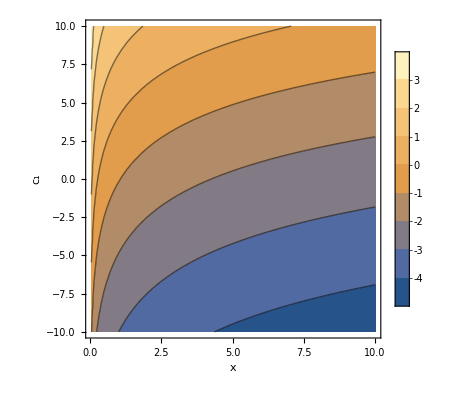

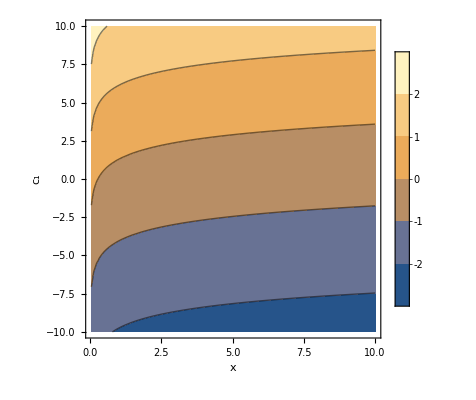

```mathematica
ContourPlot[Log[Abs[Eq213THC2S1B1]]/.{h->1,α->1,x->a,C[1]->b},{a,0.05,10},{b,-10,10},PlotRange->{{0.05, 10},{-10,10}},PlotLegends->Automatic,LabelStyle->Directive[Black,15],FrameLabel->{"x","c_1"}]
ContourPlot[Log[Abs[Eq214THC2S1B1]]/.{h->1,α->1,x->a,C[1]->b},{a,0.05,10},{b,-10,10},PlotRange->{{0.05, 10},{-10,10}},PlotLegends->Automatic,LabelStyle->Directive[Black,15],FrameLabel->{"x","c_1"}]
```

The above contour plots show that the consistency conditions are generally satisfied.

Finally, we compute the Friedmann constraint on this branch. We obtain...

```mathematica
$Assumptions=a[t]≠0;
FeqTHdsVac/.C2/.C2S1/.ϕTox/.({ℐ'[x]->y[x],ℐ''[x]->y'[x]}/.x->x[t])/.C2S1sol[[1]]//FullSimplify
```

(4 3^(2/3) ⅇ^(C[1]/2))/((√(-(12 ⅇ^((3 C[1])/2))/x[t]^(9/2)+(81 ⅇ^C[1] h^2 α^2)/x[t]^4)+(9 ⅇ^(C[1]/2) h α)/x[t]^2)^(1/3) √x[t])+9 2^(2/3) h α √x[t]+2 6^(1/3) (√(-(12 ⅇ^((3 C[1])/2))/x[t]^(9/2)+(81 ⅇ^C[1] h^2 α^2)/x[t]^4)+(9 ⅇ^(C[1]/2) h α)/x[t]^2)^(1/3) x[t]==3 2^(1/6) (6 h^2 κ-ρΛ+ℐ[x[t]]+3 h^2 α ϕ[t])

The explicit time dependence is clear. Therefore, the 1st branch solution well-tempers.

#### 3.3 A(X)+𝒢

In this section, we also showcase Teledeski’s revival of the Horndeski potential G_4=A(ϕ,X) and explicitly show well-tempering in this revived Horndeski sector of the theory. We begin by writing down the degeneracy and consistency conditions...

```mathematica
C3={G2->Function[{a,b},0],G3->Function[{a,b},0]};

ϕTox=Solve[{x[t]==ϕ'[t]^2/2,x'[t]==D[(ϕ'[t]^2/2), t]},{ϕ'[t],ϕ''[t]}][[2]];

Eq211THC3=Eq211TH/.C3/.ϕTox//Simplify;
Eq213THC3=Eq213TH[[1]]/.C3/.ϕTox//Simplify;
Eq214THC3=Eq214TH[[1]]/.C3/.ϕTox//Simplify;

Eq211THC3/.SimpTH
Eq213THC3≠0/.SimpTH
Eq214THC3≠0/.SimpTH
```

√2 √x[t] (3 h^2 A^(0,1)+12 h^2 x[t]^2 A^(0,3)-6 √2 h x[t]^(3/2) A^(1,2)+9 h^2 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0)+𝒢^(0,1,0,0,0,0,0,0,0,0,0,0)+3 √2 h √x[t] (-3 A^(1,1)+2 𝒢^(0,1,0,0,0,1,0,0,0,0,0,0))+2 x[t] (12 h^2 A^(0,2)+𝒢^(0,2,0,0,0,0,0,0,0,0,0,0))) (6 √2 h^2 x[t]^(3/2) A^(0,2)-10 h x[t] A^(1,1)+√2 √x[t] (3 h^2 A^(0,1)+A^(2,0)+𝒢^(0,1,0,0,0,0,0,0,0,0,0,0)-𝒢^(1,0,0,0,0,1,0,0,0,0,0,0))-h (A^(1,0)-3 𝒢^(0,0,0,0,0,1,0,0,0,0,0,0)-6 𝒢^(1,0,0,0,1,0,0,0,0,0,0,0)+4 𝒢^(1,0,1,0,0,0,0,0,0,0,0,0)))==(-4 √2 h x[t]^(3/2) A^(0,2)+A^(1,0)-𝒢^(0,0,0,0,0,1,0,0,0,0,0,0)+18 h^2 𝒢^(0,0,0,0,1,1,0,0,0,0,0,0)-12 h^2 𝒢^(0,0,1,0,0,1,0,0,0,0,0,0)+2 x[t] (A^(1,1)-𝒢^(0,1,0,0,0,1,0,0,0,0,0,0))-√2 h √x[t] (2 A^(0,1)+3 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0)-6 𝒢^(0,1,0,0,1,0,0,0,0,0,0,0)+4 𝒢^(0,1,1,0,0,0,0,0,0,0,0,0))) (-6 h^2 A^(1,0)+12 h^2 x[t]^2 A^(1,2)+6 √2 h x[t]^(3/2) (3 h^2 A^(0,2)-A^(2,1))+9 h^2 𝒢^(0,0,0,0,0,1,0,0,0,0,0,0)-𝒢^(1,0,0,0,0,0,0,0,0,0,0,0)+3 √2 h √x[t] (3 h^2 A^(0,1)+𝒢^(0,1,0,0,0,0,0,0,0,0,0,0)+𝒢^(1,0,0,0,0,1,0,0,0,0,0,0))+2 x[t] (-9 h^2 A^(1,1)+𝒢^(1,1,0,0,0,0,0,0,0,0,0,0)))

-3 h^2 A^(0,1)-12 h^2 x[t]^2 A^(0,3)+6 √2 h x[t]^(3/2) A^(1,2)-9 h^2 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0)-𝒢^(0,1,0,0,0,0,0,0,0,0,0,0)+3 √2 h √x[t] (3 A^(1,1)-2 𝒢^(0,1,0,0,0,1,0,0,0,0,0,0))-2 x[t] (12 h^2 A^(0,2)+𝒢^(0,2,0,0,0,0,0,0,0,0,0,0))≠0

-4 √2 h x[t]^(3/2) A^(0,2)+A^(1,0)-𝒢^(0,0,0,0,0,1,0,0,0,0,0,0)+18 h^2 𝒢^(0,0,0,0,1,1,0,0,0,0,0,0)-12 h^2 𝒢^(0,0,1,0,0,1,0,0,0,0,0,0)+2 x[t] (A^(1,1)-𝒢^(0,1,0,0,0,1,0,0,0,0,0,0))-√2 h √x[t] (2 A^(0,1)+3 𝒢^(0,0,0,0,0,2,0,0,0,0,0,0)-6 𝒢^(0,1,0,0,1,0,0,0,0,0,0,0)+4 𝒢^(0,1,1,0,0,0,0,0,0,0,0,0))≠0

As a first special case, we consider the shift symmetric sector...

```mathematica
C3S1={A->Function[{a,b},A[b]],𝒢->Function[{A,B,C,D,e,F,G,H,I,J,K,L},g[B]+ℐ[F^2/(2(3h)^2)]]};

Eq211THC3S1=Eq211THC3/.C3S1/.{ϕ[t]->ϕ,x[t]->x}//Simplify;
Eq213THC3S1=Eq213THC3/.C3S1/.{ϕ[t]->ϕ,x[t]->x}//Simplify;
Eq214THC3S1=Eq214THC3/.C3S1/.{ϕ[t]->ϕ,x[t]->x}//Simplify;

Eq211THC3S1
Eq213THC3S1≠0
Eq214THC3S1≠0
```

x (3 h^2 A'[x]+g'[x]+ℐ'[x]+6 h^2 x A''[x]) (9 h^2 A'[x]+g'[x]+3 ℐ'[x]+36 h^2 x A''[x]+2 x g''[x]+4 x ℐ''[x]+12 h^2 x^2 A^(3)[x])==0

-3 h^2 A'[x]-g'[x]-ℐ'[x]-24 h^2 x A''[x]-2 x g''[x]-2 x ℐ''[x]-12 h^2 x^2 A^(3)[x]≠0

-(2 √2 √x (3 h^2 A'[x]+ℐ'[x]+x (6 h^2 A''[x]+ℐ''[x])))/(3 h)≠0

There are two branches in the degeneracy equation. We obtain their solutions as follows...

```mathematica
C3S1sol1=DSolve[3 h^2 A'[x]+g'[x]+ℐ'[x]+6 h^2 x A''[x]==0,ℐ,x][[1]];
C3S1sol2=DSolve[Integrate[9 h^2 A'[x]+g'[x]+3 ℐ'[x]+36 h^2 x A''[x]+2 x g''[x]+4 x ℐ''[x]+12 h^2 x^2 Derivative[3][A][x],x]==C[1],ℐ,x][[1]];

ℐ[x]==(ℐ[x]/.C3S1sol1)
ℐ[x]==(ℐ[x]/.C3S1sol2)
```

ℐ[x]==3 h^2 A[x]+C[1]-g[x]-6 h^2 x A'[x]

ℐ[x]==x^(1/4) C[2]+x^(1/4) ∫_1^x 1/(4 K[1]^(5/4))(3 h^2 A[K[1]]+C[1]+g[K[1]]-12 h^2 K[1] A'[K[1]]-2 K[1] g'[K[1]]-12 h^2 K[1]^2 A''[K[1]])ⅆK[1]

Using these analytical solutions, we can evaluate the consistency conditions for both branches. We obtain...

```mathematica
(* branch 1 *)
Eq213THC3S1/.C3S1sol1//Simplify
Eq214THC3S1/.C3S1sol1//Simplify

(* branch 2 *)
Eq213THC3S1/.C3S1sol2//Simplify
Eq214THC3S1/.C3S1sol2//Simplify
```

0

(2 √2 √x (g'[x]+x (9 h^2 A''[x]+g''[x]+6 h^2 x A^(3)[x])))/(3 h)

1/(8 x)(3 h^2 A[x]+C[1]+x^(1/4) C[2]+g[x]+x^(1/4) ∫_1^x 1/(4 K[1]^(5/4))(3 h^2 A[K[1]]+C[1]+g[K[1]]-12 h^2 K[1] A'[K[1]]-2 K[1] g'[K[1]]-12 h^2 K[1]^2 A''[K[1]])ⅆK[1]-6 x g'[x]-60 h^2 x^2 A''[x]-8 x^2 g''[x]-48 h^2 x^3 A^(3)[x])

1/(12 √2 h √x)(-3 h^2 A[x]-C[1]-x^(1/4) C[2]-g[x]-x^(1/4) ∫_1^x 1/(4 K[1]^(5/4))(3 h^2 A[K[1]]+C[1]+g[K[1]]-12 h^2 K[1] A'[K[1]]-2 K[1] g'[K[1]]-12 h^2 K[1]^2 A''[K[1]])ⅆK[1]+6 x g'[x]+60 h^2 x^2 A''[x]+8 x^2 g''[x]+48 h^2 x^3 A^(3)[x])

The first branch obviously cannot well-temper. As for the 2nd branch, the Friedmann constraint becomes...

```mathematica
FeqTHdsVac/.C3/.C3S1/.ϕTox/.C3S1sol2//Simplify
```

6 h^2 κ==ρΛ+C[1]

The Friedmann constraint reduces to just a bunch of constants on-shell. The 2nd branch therefore tunes away vacuum energy, but not through well-tempering.

We move on to a second special case that may well-temper...

```mathematica
C3S2={A->Function[{a,b},A[b]],𝒢->Function[{A,B,C,D,e,F,G,H,I,J,K,L},l A+g[B]+ℐ[F^2/(2(3h)^2)]]};

Eq211THC3S2=Eq211THC3/.C3S2/.{ϕ[t]->ϕ,x[t]->x}//Simplify;
Eq213THC3S2=Eq213THC3/.C3S2/.{ϕ[t]->ϕ,x[t]->x}//Simplify;
Eq214THC3S2=Eq214THC3/.C3S2/.{ϕ[t]->ϕ,x[t]->x}//Simplify;

Eq211THC3S2
Eq213THC3S2≠0
Eq214THC3S2≠0
```

2 x (3 h^2 A'[x]+g'[x]+ℐ'[x]+6 h^2 x A''[x]) (3 h^2 A'[x]+g'[x]+ℐ'[x]+24 h^2 x A''[x]+2 x g''[x]+2 x ℐ''[x]+12 h^2 x^2 A^(3)[x])==-1/(3 h)2 √2 √x (-l+9 √2 h^3 √x A'[x]+3 √2 h √x g'[x]+3 √2 h √x ℐ'[x]+18 √2 h^3 x^(3/2) A''[x]) (3 h^2 A'[x]+ℐ'[x]+x (6 h^2 A''[x]+ℐ''[x]))

-3 h^2 A'[x]-g'[x]-ℐ'[x]-24 h^2 x A''[x]-2 x g''[x]-2 x ℐ''[x]-12 h^2 x^2 A^(3)[x]≠0

-(2 √2 √x (3 h^2 A'[x]+ℐ'[x]+x (6 h^2 A''[x]+ℐ''[x])))/(3 h)≠0

To solve this, we take an ansatz inspired from the previous solution:

```mathematica
C3S2ansatz={ℐ->Function[{x},3 h^2 A[x]+C[1]-g[x]-6 h^2 x A'[x]+ξ[x]]};
```

In this equation, ξ is an arbitrary function that parametrizes the space of well-tempered theories. To determine the Horndeski potential A, we now put back the ansatz into the degeneracy equation...

```mathematica
Eq211THC3S2/.C3S2ansatz//Simplify
```

2 x ξ'[x] (ξ'[x]+2 x ξ''[x])==1/(3 h)2 √2 √x (-l+3 √2 h √x ξ'[x]) (g'[x]-ξ'[x]+x (9 h^2 A''[x]+g''[x]-ξ''[x]+6 h^2 x A^(3)[x]))

This can be solved by noting that this is a first-order differential equation in A''(x). This leads to...

```mathematica
C3S2sol=DSolve[Eq211THC3S2/.C3S2ansatz/.{A''[x]->y[x],Derivative[3][A][x]->y'[x]}//Simplify,y,x][[1]];

A''[x]==(y[x]/.C3S2sol)
```

A''[x]==C[1]/x^(3/2)+1/x^(3/2)(∫_1^x ((√2 l g'[K[1]]-√2 l ξ'[K[1]]-6 h √K[1] g'[K[1]] ξ'[K[1]]+9 h √K[1] ξ'[K[1]]^2+√2 l K[1] g''[K[1]]-6 h K[1]^(3/2) ξ'[K[1]] g''[K[1]]-√2 l K[1] ξ''[K[1]]+12 h K[1]^(3/2) ξ'[K[1]] ξ''[K[1]])/(6 h^2 √K[1] (-√2 l+6 h √K[1] ξ'[K[1]])))ⅆK[1])

The consistency conditions become...

```mathematica
(Eq213THC3S2/.C3S2ansatz/.{A''[x]->y[x],Derivative[3][A][x]->y'[x]}/.C3S2sol//Simplify)≠0
(Eq214THC3S2/.C3S2ansatz/.{A''[x]->y[x],Derivative[3][A][x]->y'[x]}/.C3S2sol//Simplify)≠0
```

-ξ'[x]-2 x ξ''[x]≠0

-(2 √2 x ξ'[x] (ξ'[x]+2 x ξ''[x]))/(√2 l-6 h √x ξ'[x])≠0

The consistency conditions are therefore satisfied as long as ξ(x) does not satisfy 2x ξ''(x)+ξ'(x)=0 or rather...

```mathematica
DSolve[ξ'[x]+2 x ξ''[x]==0,ξ,x][[1]]
```

{ξ→Function[{x},2 √x C[1]+C[2]]}

The Hamiltonian constraint on-shell must also be checked. This leads to...

```mathematica
FeqTHdsVac/.C3/.C3S2/.ϕTox/.C3S2ansatz/.({A''[x]->y[x],Derivative[3][A][x]->y'[x]}/.x->x[t])/.C3S2sol//Simplify
```

6 h^2 κ+6 h^2 A[x[t]]+C[1]+12 h^2 (C[1]+∫_1^x[t] ((9 h √K[1] ξ'[K[1]]^2+g'[K[1]] (√2 l-6 h √K[1] ξ'[K[1]])+√2 l K[1] (g''[K[1]]-ξ''[K[1]])-ξ'[K[1]] (√2 l+6 h K[1]^(3/2) g''[K[1]]-12 h K[1]^(3/2) ξ''[K[1]]))/(-6 √2 h^2 l √K[1]+36 h^3 K[1] ξ'[K[1]]))ⅆK[1]) √x[t]+ξ[x[t]]+l ϕ[t]+x[t] (-6 h^2 A'[x[t]]+2 g'[x[t]]-4 ξ'[x[t]])==ρΛ

Unfortunately, this could not be simplified further, and so it is difficult to assess whether an explicit time dependence remains in the Hamiltonian constraint. Nonetheless, we can proceed by simply substituting explicit choices for the free functions g and ℐ to confirm well-tempering. In this direction, we can obtain A(x)...

```mathematica
C3S2special={g->Function[x,β x],ξ->Function[x,γ x]};

C3S2solspecial=DSolve[Eq211THC3S2/.C3S2ansatz/.C3S2special//Simplify,A,x][[1]];

A[x]==(A[x]/.C3S2solspecial)
```

A[x]==C[2]+x C[3]-1/(18 h^3)(-6 h x (β-γ)+√x (-√2 l+72 h^3 C[1])+6 h x (β-γ) Log[x]+2 √x (√2 l-3 h √x γ) Log[√2 l-6 h √x γ]-(l^2 Log[-√2 l+6 h √x γ])/(3 h γ)-3 h x γ (-1+2 (-Log[√2 l-6 h √x γ]+Log[-√2 l+6 h √x γ])))

The consistency conditions and the Hamiltonian constraint can be shown to be...

```mathematica
(* consistency condition *)
(Eq213THC3S2/.C3S2ansatz/.C3S2special/.C3S2solspecial//Simplify)≠0
(Eq214THC3S2/.C3S2ansatz/.C3S2special/.C3S2solspecial//Simplify)≠0

(* Hamiltonian constraint *)
FeqTHdsVac/.C3/.C3S2/.ϕTox/.C3S2ansatz/.C3S2special/.C3S2solspecial//Simplify
```

-γ≠0

-(4 √2 x γ^2 (l^2-6 √2 h l √x γ+18 h^2 x γ^2))/(√2 l-6 h √x γ)^3≠0

(54 √2 h^3 l γ^3 x[t]^(3/2)+18 h^2 γ^2 x[t] (-2 l^2+54 h^4 γ κ-9 h^2 γ ρΛ+9 h^2 γ C[1]+54 h^4 γ C[2]+l^2 Log[-√2 l+6 h γ √x[t]]+9 h^2 l γ ϕ[t])+l^2 (9 h^2 γ (-ρΛ+C[1]+6 h^2 (κ+C[2]))+l^2 Log[-√2 l+6 h γ √x[t]]+9 h^2 l γ ϕ[t])-3 √2 h l γ √x[t] (-l^2+108 h^4 γ κ-18 h^2 γ ρΛ+18 h^2 γ C[1]+108 h^4 γ C[2]+2 l^2 Log[-√2 l+6 h γ √x[t]]+18 h^2 l γ ϕ[t]))/(h γ (-√2 l+6 h γ √x[t]))==0

This shows that well-tempering is possible in this sector.

#### 3.4 A(X)+V(X)+G(X)+𝒢

In this section, we derive closed-form expressions to well-tempered cosmology in the shift symmetric sector in Teledeski gravity...

```mathematica
TeledeskiSS={G2->Function[{a,b},l a+V[b]],G3->Function[{a,b},G[b]],A->Function[{a,b},A[b]],𝒢->Function[{A,B,C,D,e,F,G,H,I,J,K,L},𝒬[B]ℐ[F^2/(2(3h)^2)]]};
```

We start by parametrizing the solutions of the degeneracy equation as...

```mathematica
$Assumptions=a[t]>0;
ϕTox=Solve[{x[t]==ϕ'[t]^2/2,x'[t]==D[(ϕ'[t]^2/2), t]},{ϕ'[t],ϕ''[t]}][[2]];
fToq=f->Function[x,q[x^2/2]/x];

Eq1T4SS=f[ϕ'[t]](𝒵/(3 a[t]^2))==𝒟/a[t]^3/.TeledeskiSS/.fToq/.ϕTox/.x[t]->x//Simplify;
Eq2T4SS=f[ϕ'[t]](𝒴/(3 a[t]^2))==𝒞/a[t]^3/.TeledeskiSS/.fToq/.ϕTox/.x[t]->x//Simplify;

Eq1T4SS
Eq2T4SS
```

3 h^2 A'[x]+6 √2 h √x G'[x]+V'[x]+𝒬[x] ℐ'[x]+ℐ[x] 𝒬'[x]+4 x ℐ'[x] 𝒬'[x]+24 h^2 x A''[x]+6 √2 h x^(3/2) G''[x]+2 x V''[x]+2 x 𝒬[x] ℐ''[x]+2 x ℐ[x] 𝒬''[x]+12 h^2 x^2 A^(3)[x]==1/(3 h)q[x] (6 h^2 A'[x]+3 √2 h √x G'[x]+2 (𝒬[x] ℐ'[x]+x ℐ'[x] 𝒬'[x]+6 h^2 x A''[x]+x 𝒬[x] ℐ''[x]))

√x (3 h+q[x]) (3 √2 h^2 A'[x]+6 h √x G'[x]+√2 (V'[x]+𝒬[x] ℐ'[x]+ℐ[x] 𝒬'[x]+6 h^2 x A''[x]))==l

To solve the above system, we make the potential redefinition to 𝒦...

```mathematica
VGTo𝒦0=V'[x]->-3h √(2x)G'[x]+𝒦[x];
VGTo𝒦1=Solve[D[(V'[x]), x]==D[(-3h √(2x)G'[x]+𝒦[x]), x],V''[x]][[1]];

Eq1T4SS/.VGTo𝒦0/.VGTo𝒦1//Simplify
Eq2T4SS/.VGTo𝒦0/.VGTo𝒦1//Simplify
```

𝒦[x]+3 h^2 A'[x]+𝒬[x] ℐ'[x]+2 x 𝒦'[x]+ℐ[x] 𝒬'[x]+4 x ℐ'[x] 𝒬'[x]+24 h^2 x A''[x]+2 x 𝒬[x] ℐ''[x]+2 x ℐ[x] 𝒬''[x]+12 h^2 x^2 A^(3)[x]==1/(3 h)q[x] (6 h^2 A'[x]+3 √2 h √x G'[x]+2 (𝒬[x] ℐ'[x]+x ℐ'[x] 𝒬'[x]+6 h^2 x A''[x]+x 𝒬[x] ℐ''[x]))

√2 √x (3 h+q[x]) (𝒦[x]+3 h^2 A'[x]+𝒬[x] ℐ'[x]+ℐ[x] 𝒬'[x]+6 h^2 x A''[x])==l

The second equation can be solved for 𝒦(x)...

```mathematica
𝒦T4SS=Solve[Eq2T4SS/.VGTo𝒦0/.VGTo𝒦1//Simplify,𝒦[x]][[1]];

𝒦[x]==Collect[𝒦[x]/.𝒦T4SS,{Derivative[u_][ℐ][x_],Derivative[u_][A][x_],l},Simplify]
```

𝒦[x]==l/(√2 √x (3 h+q[x]))-3 h^2 A'[x]-𝒬[x] ℐ'[x]-ℐ[x] 𝒬'[x]-6 h^2 x A''[x]

The braiding G_X can then be obtained as...

```mathematica
GwtT4SS=Solve[(Eq1T4SS/.VGTo𝒦0/.VGTo𝒦1//Simplify)/.𝒦T4SS/.(𝒦'[x]->D[(𝒦[x]/.𝒦T4SS), x])//Simplify,G'[x]][[1]]//Simplify;

G'[x]==Collect[G'[x]/.GwtT4SS,{Derivative[u_][ℐ][x_],Derivative[u_][A][x_],l},Simplify]
```

G'[x]==-(√2 h A'[x])/(√x)-(l q'[x])/(q[x] (3 h+q[x])^2)-(√2 ℐ'[x] (𝒬[x]+x 𝒬'[x]))/(3 h √x)-2 √2 h √x A''[x]-(√2 √x 𝒬[x] ℐ''[x])/(3 h)

With this, the k-essence potential also follows...

```mathematica
VwtT4SS={V'[x]->(V'[x]/.VGTo𝒦0/.𝒦T4SS/.GwtT4SS//Simplify)};

V'[x]==Collect[V'[x]/.VwtT4SS,{Derivative[u_][ℐ][x_],Derivative[u_][A][x_],l},Simplify]
```

V'[x]==3 h^2 A'[x]+(l (3 h q[x]+q[x]^2+6 h x q'[x]))/(√2 √x q[x] (3 h+q[x])^2)-ℐ[x] 𝒬'[x]+ℐ'[x] (𝒬[x]+2 x 𝒬'[x])+6 h^2 x A''[x]+2 x 𝒬[x] ℐ''[x]

The above solutions for the functionals V[q,A,𝒬,ℐ] and G[q,A,𝒬,ℐ] describe the most general well-tempered models of shift symmetric theories in Teledeski gravity up to G_4(X). It can be further confirmed that the Friedmann constraint on-shell is time dependent...

```mathematica
$Assumptions=ϕ'[t]>0;
FeqT4SSdSvac=Collect[FeqTHdsVac[[1]]-FeqTHdsVac[[2]]/.TeledeskiSS/.ϕTox/.GwtT4SS/.VwtT4SS/.ρ[t]->ρΛ//Simplify,{a[t],ℐ[x_],Derivative[u_][ℐ][x_],Derivative[u_][A][x_],l},Simplify]==0;

FeqT4SSdSvac
```

a[t]^3 (6 h^2 κ-ρΛ+3 h^2 A[x[t]]+V[x[t]]+l ϕ[t]-12 h^2 x[t] A'[x[t]]-6 √2 h x[t]^(3/2) G'[x[t]]-2 x[t] V'[x[t]]-4 x[t] 𝒬[x[t]] ℐ'[x[t]]+ℐ[x[t]] (𝒬[x[t]]-2 x[t] 𝒬'[x[t]])-12 h^2 x[t]^2 A''[x[t]])==0

Vacuum energy is being dynamically cancelled, i.e., no tuning of mass scales. The Hubble and the scalar field equations also simplify into a Riccati equation in the vacuum...

```mathematica
HeqT4SSdSvac=Collect[HeqTHdsVac[[1]]-HeqTHdsVac[[2]]/.TeledeskiSS/.ϕTox/.(GwtT4SS/.x->x[t])/.(VwtT4SS/.x->x[t])//Simplify,{ℐ[x_],Derivative[u_][ℐ][x_],Derivative[u_][A][x_],l},Simplify]==0;
SeqT4SSdSvac=Collect[SeqTHdsVac[[1]]-SeqTHdsVac[[2]]/.TeledeskiSS/.ϕTox/.(GwtT4SS/.x->x[t])/.(VwtT4SS/.x->x[t])/.((G''[x]->(D[(G'[x]/.GwtT4SS), x]//Simplify))/.x->x[t])/.((V''[x]->(D[(V'[x]/.VwtT4SS), x]//Simplify))/.x->x[t])//Simplify,{ℐ[x_],Derivative[u_][ℐ][x_],Derivative[u_][A][x_],l},Simplify]==0;

HeqT4SSdSvac
SeqT4SSdSvac
```

(3 √2 l a[t]^2 √x[t] (3 h q[x[t]]+q[x[t]]^2+q'[x[t]] x'[t]))/(q[x[t]] (3 h+q[x[t]])^2)==0

(l a[t]^3 (3 h q[x[t]]+q[x[t]]^2+q'[x[t]] x'[t]))/(3 h+q[x[t]])^2==0

The explicit Riccati equation can be obtained by noting that q'(X)ϕ̇ ϕ^(..)=q̇=d q/d t. This leads to the exact closed-form solution...

```mathematica
RiccatiEq=q'[t]+3h q[t]+q[t]^2==0;
RiccatiSol=DSolve[RiccatiEq,q,t][[1]]/.C[1]->𝒯;

RiccatiEq
q[t]==(q[t]/.RiccatiSol)
```

3 h q[t]+q[t]^2+q'[t]==0

q[t]==(3 h)/(-1+ⅇ^(3 h (t-𝒯)))

This is an implicit solution to well-tempered cosmology in the shift symmetric sector. For example, after providing q(x), the above equation can be used to algebraically obtain the scalar field derivative ϕ̇(t), and consequently, the scalar field ϕ(t) itself.

#### 3.5 The No-Tempering Theorem

In this section, we revise the no-tempering theorem in tadpole-free (l=0) shift symmetric sector to include TG. To start, we write down the most general, tadpole-free, shift symmetric theory...

```mathematica
(* linear as in arXiv:2009.01720 (Eq. 3.8) *)
C5={G2->Function[{ϕ,X},V[X]],G3->Function[{ϕ,X},G[X]],A->Function[{ϕ,X},A[X]],𝒢->Function[{A,B,C,D,e,F,G,H,I,J,K,L},𝒬[B]ℐ[F^2/(2(3h)^2)]]};

$Assumptions=a[t]>0;
ϕTox=Solve[{x[t]==ϕ'[t]^2/2,x'[t]==D[(ϕ'[t]^2/2), t]},{ϕ'[t],ϕ''[t]}][[2]];

Eq211THC5=Eq211TH[[1]]/.C5/.ϕTox/.x[t]->x//Simplify;
Eq213THC5=Eq213TH[[1]]/.C5/.ϕTox/.x[t]->x//Simplify;
Eq214THC5=Eq214TH[[1]]/.C5/.ϕTox/.x[t]->x//Simplify;

Eq211THC5==0/.SimpTH
Eq213THC5≠0/.SimpTH
Eq214THC5≠0/.SimpTH
```

x (3 √2 h^2 A'[x]+6 h √x G'[x]+√2 (V'[x]+𝒬[x] ℐ'[x]+ℐ[x] 𝒬'[x]+6 h^2 x A''[x])) (9 √2 h^2 A'[x]+18 h √x G'[x]+√2 V'[x]+3 √2 𝒬[x] ℐ'[x]+√2 ℐ[x] 𝒬'[x]+6 √2 x ℐ'[x] 𝒬'[x]+36 √2 h^2 x A''[x]+12 h x^(3/2) G''[x]+2 √2 x V''[x]+4 √2 x 𝒬[x] ℐ''[x]+2 √2 x ℐ[x] 𝒬''[x]+12 √2 h^2 x^2 A^(3)[x])==0

-3 h^2 A'[x]-6 √2 h √x G'[x]-V'[x]-𝒬[x] ℐ'[x]-ℐ[x] 𝒬'[x]-4 x ℐ'[x] 𝒬'[x]-24 h^2 x A''[x]-6 √2 h x^(3/2) G''[x]-2 x V''[x]-2 x 𝒬[x] ℐ''[x]-2 x ℐ[x] 𝒬''[x]-12 h^2 x^2 A^(3)[x]≠0

-1/(3 h)2 √x (3 √2 h^2 A'[x]+3 h √x G'[x]+√2 (𝒬[x] ℐ'[x]+x ℐ'[x] 𝒬'[x]+6 h^2 x A''[x]+x 𝒬[x] ℐ''[x]))≠0

The two branches of the degeneracy equation can now be solved easily...

```mathematica
C5sol1=DSolve[3 √2 h^2 A'[x]+6 h √x G'[x]+√2 (V'[x]+𝒬[x] ℐ'[x]+ℐ[x] 𝒬'[x]+6 h^2 x A''[x])==0,ℐ,x][[1]];
C5sol2=DSolve[Integrate[9 √2 h^2 A'[x]+18 h √x G'[x]+√2 V'[x]+3 √2 𝒬[x] ℐ'[x]+√2 ℐ[x] 𝒬'[x]+6 √2 x ℐ'[x] 𝒬'[x]+36 √2 h^2 x A''[x]+12 h x^(3/2) G''[x]+2 √2 x V''[x]+4 √2 x 𝒬[x] ℐ''[x]+2 √2 x ℐ[x] 𝒬''[x]+12 √2 h^2 x^2 Derivative[3][A][x],x]==C[1],ℐ,x][[1]];

ℐ[x]==(ℐ[x]/.C5sol1)
ℐ[x]==(ℐ[x]/.C5sol2)
```

ℐ[x]==C[1]/𝒬[x]+(∫_1^x -(3 √2 h^2 A'[K[1]]+6 h √K[1] G'[K[1]]+√2 V'[K[1]]+6 √2 h^2 K[1] A''[K[1]])/(√2)ⅆK[1])/𝒬[x]

ℐ[x]==(x^(1/4) C[2])/(√𝒬[x])+1/(√𝒬[x])x^(1/4) ∫_1^x -((-3 √2 h^2 A[K[1]]-C[1]-√2 V[K[1]]+12 √2 h^2 K[1] A'[K[1]]+12 h K[1]^(3/2) G'[K[1]]+2 √2 K[1] V'[K[1]]+12 √2 h^2 K[1]^2 A''[K[1]])/(4 √2 K[1]^(5/4) √𝒬[K[1]]))ⅆK[1]

To assess whether the two solutions lead to well-tempered cosmology, we put them back into the consistency conditions. This leads to...

```mathematica
(* branch 1 *)
Eq213THC5/.C5sol1//Simplify
Eq214THC5/.C5sol1//Simplify

(* branch 2*)
Eq213THC5/.C5sol2//Simplify
Eq214THC5/.C5sol2//Simplify
```

0

1/(3 h 𝒬[x]^2)2 √x (-√2 x (C[1]+∫_1^x (-3 h^2 A'[K[1]]-3 √2 h √K[1] G'[K[1]]-V'[K[1]]-6 h^2 K[1] A''[K[1]])ⅆK[1]) 𝒬'[x]^2+𝒬[x] (𝒬'[x] (√2 C[1]+√2 ∫_1^x (-3 h^2 A'[K[1]]-3 √2 h √K[1] G'[K[1]]-V'[K[1]]-6 h^2 K[1] A''[K[1]])ⅆK[1]-3 √2 h^2 x A'[x]-6 h x^(3/2) G'[x]-√2 x V'[x]-6 √2 h^2 x^2 A''[x])+√2 x (C[1]+∫_1^x (-3 h^2 A'[K[1]]-3 √2 h √K[1] G'[K[1]]-V'[K[1]]-6 h^2 K[1] A''[K[1]])ⅆK[1]) 𝒬''[x])+𝒬[x]^2 (6 h √x G'[x]+√2 V'[x]+x (9 √2 h^2 A''[x]+6 h √x G''[x]+√2 (V''[x]+6 h^2 x A^(3)[x]))))

1/(16 x 𝒬[x]^(3/2))(2 x^(1/4) (C[2]+∫_1^x ((3 √2 h^2 A[K[1]]+C[1]+√2 V[K[1]]-12 √2 h^2 K[1] A'[K[1]]-12 h K[1]^(3/2) G'[K[1]]-2 √2 K[1] V'[K[1]]-12 √2 h^2 K[1]^2 A''[K[1]])/(4 √2 K[1]^(5/4) √𝒬[K[1]]))ⅆK[1]) 𝒬[x]^2+8 x^(9/4) (C[2]+∫_1^x ((3 √2 h^2 A[K[1]]+C[1]+√2 V[K[1]]-12 √2 h^2 K[1] A'[K[1]]-12 h K[1]^(3/2) G'[K[1]]-2 √2 K[1] V'[K[1]]-12 √2 h^2 K[1]^2 A''[K[1]])/(4 √2 K[1]^(5/4) √𝒬[K[1]]))ⅆK[1]) 𝒬'[x]^2+6 h^2 A[x] √𝒬[x] (𝒬[x]-2 x 𝒬'[x])+2 x √𝒬[x] 𝒬'[x] (-√2 C[1]-2 V[x]+24 h^2 x A'[x]+12 √2 h x^(3/2) G'[x]+4 x V'[x]+24 h^2 x^2 A''[x])-16 x^(5/4) (C[2]+∫_1^x ((3 √2 h^2 A[K[1]]+C[1]+√2 V[K[1]]-12 √2 h^2 K[1] A'[K[1]]-12 h K[1]^(3/2) G'[K[1]]-2 √2 K[1] V'[K[1]]-12 √2 h^2 K[1]^2 A''[K[1]])/(4 √2 K[1]^(5/4) √𝒬[K[1]]))ⅆK[1]) 𝒬[x] (𝒬'[x]+x 𝒬''[x])+𝒬[x]^(3/2) (√2 C[1]+2 V[x]-36 √2 h x^(3/2) G'[x]-12 x V'[x]-120 h^2 x^2 A''[x]-48 √2 h x^(5/2) G''[x]-16 x^2 V''[x]-96 h^2 x^3 A^(3)[x]))

1/(24 h √x 𝒬[x]^(3/2))(-√2 x^(1/4) (C[2]+∫_1^x ((3 √2 h^2 A[K[1]]+C[1]+√2 V[K[1]]-12 √2 h^2 K[1] A'[K[1]]-12 h K[1]^(3/2) G'[K[1]]-2 √2 K[1] V'[K[1]]-12 √2 h^2 K[1]^2 A''[K[1]])/(4 √2 K[1]^(5/4) √𝒬[K[1]]))ⅆK[1]) 𝒬[x]^2-4 √2 x^(9/4) (C[2]+∫_1^x ((3 √2 h^2 A[K[1]]+C[1]+√2 V[K[1]]-12 √2 h^2 K[1] A'[K[1]]-12 h K[1]^(3/2) G'[K[1]]-2 √2 K[1] V'[K[1]]-12 √2 h^2 K[1]^2 A''[K[1]])/(4 √2 K[1]^(5/4) √𝒬[K[1]]))ⅆK[1]) 𝒬'[x]^2-3 √2 h^2 A[x] √𝒬[x] (𝒬[x]-2 x 𝒬'[x])-2 x √𝒬[x] 𝒬'[x] (-C[1]-√2 V[x]+12 √2 h^2 x A'[x]+12 h x^(3/2) G'[x]+2 √2 x V'[x]+12 √2 h^2 x^2 A''[x])+8 √2 x^(5/4) (C[2]+∫_1^x ((3 √2 h^2 A[K[1]]+C[1]+√2 V[K[1]]-12 √2 h^2 K[1] A'[K[1]]-12 h K[1]^(3/2) G'[K[1]]-2 √2 K[1] V'[K[1]]-12 √2 h^2 K[1]^2 A''[K[1]])/(4 √2 K[1]^(5/4) √𝒬[K[1]]))ⅆK[1]) 𝒬[x] (𝒬'[x]+x 𝒬''[x])+𝒬[x]^(3/2) (-C[1]-√2 V[x]+36 h x^(3/2) G'[x]+6 √2 x V'[x]+60 √2 h^2 x^2 A''[x]+48 h x^(5/2) G''[x]+8 √2 x^2 V''[x]+48 √2 h^2 x^3 A^(3)[x]))

The first branch therefore does not well-temper. On  the other hand, for the second branch, we compute the Friedmann constraint on-shell. This leads to...

```mathematica
FeqTHdsVac/.C5/.ϕTox/.C5sol2//Simplify
```

12 h^2 κ==2 ρΛ+√2 C[1]

This shows that the self-tuning occurs via the tuning of mass scales in the action. The solution therefore does not well-temper. This ends the proof of the no-tempering theorem.

### IV. Dynamics of a well-tempered A(X)+V(X)+G(X)+𝒢 model

In this section, we study the dynamics of a well-tempered cosmological model.

#### 4.1 The model

We consider the shift symmetric potentials given by...

```mathematica
TeledeskiSS={G2->Function[{a,b},l a+V[b]],G3->Function[{a,b},G[b]],A->Function[{a,b},A[b]],𝒢->Function[{A,B,C,D,e,F,G,H,I,J,K,L},𝒬[B]ℐ[F^2/(2(3h)^2)]]};

(* general shift symmetric solution *)
wtSS={V'[x]->3 h^2 A'[x]+(l (3 h q[x]+q[x]^2+6 h x q'[x]))/(√2 √x q[x] (3 h+q[x])^2)-ℐ[x] 𝒬'[x]+ℐ'[x] (𝒬[x]+2 x 𝒬'[x])+6 h^2 x A''[x]+2 x 𝒬[x] ℐ''[x],G'[x]->-(√2 h A'[x])/(√x)-(l q'[x])/(q[x] (3 h+q[x])^2)-(√2 ℐ'[x] (𝒬[x]+x 𝒬'[x]))/(3 h √x)-2 √2 h √x A''[x]-(√2 √x 𝒬[x] ℐ''[x])/(3 h)};
DwtSS={V''[x]->(D[(V'[x]/.wtSS), x]//Simplify),G''[x]->(D[(G'[x]/.wtSS), x]//Simplify)};

(* the particular well-tempered theory is specified here *)
M1={q->Function[{x},-(3 γ h)/(γ-√x)],A->Function[x,α x],𝒬->Function[x,1],ℐ->Function[x,β x]};
```

The dynamical field equations are...

```mathematica
$Assumptions=a[t]>0;
ϕTox=Solve[{x[t]==ϕ'[t]^2/2,x'[t]==D[(ϕ'[t]^2/2), t]},{ϕ'[t],ϕ''[t]}][[2]];

HeqM1=Collect[HeqTH/.TeledeskiSS/.ϕTox/.(Union[wtSS,DwtSS]/.x->x[t])/.M1//Simplify,{H'[t],x'[t],ρ[t],P[t],l},FullSimplify];
SeqM1=Collect[SeqTH/.TeledeskiSS/.ϕTox/.(Union[wtSS,DwtSS]/.x->x[t])/.M1//Simplify,{H'[t],x'[t],ρ[t],P[t],l},FullSimplify];

HeqM1
SeqM1
```

18 h P[t] √x[t]+(6 √2 l H[t] (-γ+√x[t]) √x[t])/h+(36 (3 h^2 α+β) (h-H[t])^2 x[t]^(3/2))/h+18 h √x[t] ρ[t]+(12 √x[t] (6 h^2 κ-(3 h^2 α+β) x[t]) H'[t])/h+((√2 l (γ-√x[t]))/(h √x[t])+(12 (3 h^2 α+β) (h-H[t]) √x[t])/h) x'[t]==0

(18 √2 (3 h^2 α+β) (h-H[t])^2 H[t] x[t]^(3/2))/h-(6 l (H[t]^2 (γ √x[t]-x[t])+h^2 x[t]))/h+(-(12 √2 (3 h^2 α+β) (h-H[t]) x[t]^(3/2))/h+(2 l (-γ √x[t]+x[t]))/h) H'[t]+((l γ H[t])/(h √x[t])+(3 √2 (3 h^2 α+β) (h-H[t])^2 √x[t])/h) x'[t]==0

The Friedmann constraint is given by...

```mathematica
FeqM1=Collect[FeqTH/.TeledeskiSS/.ϕTox/.(Union[wtSS,DwtSS]/.x->x[t])/.M1/.V[x[t]]->(3 h^2 α+β)x[t]//Simplify,{ρ[t],l},FullSimplify];

FeqM1
```

-18 h κ H[t]^2+(3 (3 h^2 α+β) (h-3 H[t]) (h-H[t]) x[t])/h+3 h ρ[t]+(l (√2 H[t] (-γ+√x[t])-3 h^2 ϕ[t]))/h==0

Now, we consider the dynamical system to be given by the Friedmann constraint and the scalar field equation. The matter evolution can be considered by adding the appropriate contents to the dynamical system...

```mathematica
AddMatter={ρ->Function[t,6κ H[t]^2 Ω[t]],P->Function[t,w(6κ H[t]^2 Ω[t])]};

FeqM1withMatter=FeqM1/.ρ[t]->6κ h^2 λ+ρ[t]/.AddMatter;
Meq=ρ'[t]+3H[t](ρ[t]+P[t])==0/.AddMatter;

(* the dynamical system *)
FeqM1withMatter
SeqM1
Meq
```

-18 h κ H[t]^2+(3 (3 h^2 α+β) (h-3 H[t]) (h-H[t]) x[t])/h+(l (√2 H[t] (-γ+√x[t])-3 h^2 ϕ[t]))/h+3 h (6 h^2 κ λ+6 κ H[t]^2 Ω[t])==0

(18 √2 (3 h^2 α+β) (h-H[t])^2 H[t] x[t]^(3/2))/h-(6 l (H[t]^2 (γ √x[t]-x[t])+h^2 x[t]))/h+(-(12 √2 (3 h^2 α+β) (h-H[t]) x[t]^(3/2))/h+(2 l (-γ √x[t]+x[t]))/h) H'[t]+((l γ H[t])/(h √x[t])+(3 √2 (3 h^2 α+β) (h-H[t])^2 √x[t])/h) x'[t]==0

3 H[t] (6 κ H[t]^2 Ω[t]+6 w κ H[t]^2 Ω[t])+12 κ H[t] Ω[t] H'[t]+6 κ H[t]^2 Ω'[t]==0

To proceed numerically and explore different cases, we prepare the nondimensionalized version of the above dynamical system. Naturally, we can use the self-tuning parameter h itself as a length scale...

```mathematica
$Assumptions=h>0;
nd={t->τ,H[t]->h y[τ],H'[t]->h^2 y'[τ],x[t]->h^2 χ[τ],x'[t]->h^3 χ'[τ],Ω'[t]->h Ω'[τ],α->α/h^2,γ->h γ,l->h^2 l};

FeqM1nd=Collect[FeqM1withMatter/.nd//Simplify,{y'[τ],χ'[τ],Ω'[τ],l},FullSimplify];
HeqM1nd=Collect[(HeqM1[[1]]-HeqM1[[2]])/h^5/.AddMatter/.nd//Simplify,{y'[τ],χ'[τ],Ω'[τ],l},FullSimplify]==0;
SeqM1nd=Collect[(SeqM1[[1]]-SeqM1[[2]])/h^6/.nd//Simplify,{y'[τ],χ'[τ],Ω'[τ],l},FullSimplify]==0;
MeqM1nd=Collect[Meq/.nd//Simplify,{y'[τ],χ'[τ],Ω'[τ],l},FullSimplify];

FeqM1nd
HeqM1nd
SeqM1nd
MeqM1nd
```

-3 l ϕ[τ]+3 (6 κ λ+(3 α+β) χ[τ]+3 y[τ]^2 ((3 α+β) χ[τ]+2 κ (-1+Ω[τ])))==√2 l y[τ] (γ-√χ[τ])+12 (3 α+β) y[τ] χ[τ]

(6 √2 l y[τ] (-γ+√χ[τ]) √χ[τ])/h+(36 √χ[τ] ((3 α+β) (-1+y[τ])^2 χ[τ]+3 (1+w) κ y[τ]^2 Ω[τ]))/h-(12 √χ[τ] (-6 κ+(3 α+β) χ[τ]) y'[τ])/h+((√2 l (γ-√χ[τ]))/(h √χ[τ])-(12 (3 α+β) (-1+y[τ]) √χ[τ])/h) χ'[τ]==0

(18 √2 (3 α+β) (-1+y[τ])^2 y[τ] χ[τ]^(3/2))/h-(6 l (y[τ]^2 (γ √χ[τ]-χ[τ])+χ[τ]))/h+((12 √2 (3 α+β) (-1+y[τ]) χ[τ]^(3/2))/h+(2 l (-γ √χ[τ]+χ[τ]))/h) y'[τ]+((l γ y[τ])/(h √χ[τ])+(3 √2 (3 α+β) (-1+y[τ])^2 √χ[τ])/h) χ'[τ]==0

3 (1+w) κ y[τ]^3 Ω[τ]+2 κ y[τ] Ω[τ] y'[τ]+κ y[τ]^2 Ω'[τ]==0

Numerical analysis can be done with this nondimensionalized system of equations.

#### 4.2 Dynamical stability of the self-tuning vacuum

We consider the case with only pure vacuum energy and without any dark/visible matter Ω=0. The dynamical system in this case can be considered to be...

```mathematica
FeqM1ndNoMat=FeqM1nd/.Ω->Function[t,0];
SeqM1ndNoMat=SeqM1nd/.Ω->Function[t,0];

FeqM1ndNoMat
SeqM1ndNoMat
```

-3 l ϕ[τ]+3 (6 κ λ+(3 α+β) χ[τ]+3 y[τ]^2 (-2 κ+(3 α+β) χ[τ]))==√2 l y[τ] (γ-√χ[τ])+12 (3 α+β) y[τ] χ[τ]

(18 √2 (3 α+β) (-1+y[τ])^2 y[τ] χ[τ]^(3/2))/h-(6 l (y[τ]^2 (γ √χ[τ]-χ[τ])+χ[τ]))/h+((12 √2 (3 α+β) (-1+y[τ]) χ[τ]^(3/2))/h+(2 l (-γ √χ[τ]+χ[τ]))/h) y'[τ]+((l γ y[τ])/(h √χ[τ])+(3 √2 (3 α+β) (-1+y[τ])^2 √χ[τ])/h) χ'[τ]==0

To look at the dynamical stability of the vacuum, we first look at the on-shell limit...

```mathematica
FeqM1ndNoMat/.y->Function[τ,1]/.χ->Function[τ,ϕ'[τ]^2/2]//Simplify
SeqM1ndNoMat/.y->Function[τ,1]/.χ->Function[τ,ϕ'[τ]^2/2]//Simplify
```

18 κ (-1+λ)+l (-√2 γ+√(ϕ'[τ]^2))==3 l ϕ[τ]

(l γ ϕ'[τ] (3 ϕ'[τ]-ϕ''[τ]))/(√(ϕ'[τ]^2))==0

In this case, we find the exact solution and the Hamiltonian constraint...

```mathematica
χM1OnShell=DSolve[SeqM1ndNoMat/.y->Function[τ,1]/.χ->Function[τ,ϕ'[τ]^2/2]//Simplify,ϕ,τ][[2]]/.{C[1]->a[1],C[2]->a[2]};

(* solution *)
ϕ[τ]==(ϕ[τ]/.χM1OnShell)

(* Hamiltonian constraint on-shell *)
FeqM1ndNoMat/.y->Function[τ,1]/.χ->Function[τ,ϕ'[τ]^2/2]/.√(ϕ'[τ]^2)->ϕ'[τ]/.χM1OnShell//Simplify
```

ϕ[τ]==1/3 ⅇ^(3 τ) a[1]+a[2]

l (√2 γ+3 a[2])==18 κ (-1+λ)

We now expand about the on-shell solution. This is setup as follows...

```mathematica
ϕyPert={ϕ->Function[τ,1/3 ⅇ^(3 τ) a[1]+a[2]+ϵ δϕ[τ]],y->Function[τ,1+ϵ δy[τ]]};
ϕyLinear[expr_]:=Collect[Series[expr/.ϕyPert,{ϵ,0,1}]//Normal,ϵ,Simplify]
```

Expanding the Friedmann and scalar field equations, we obtain...

```mathematica
FeqM1ndNoMatPert=FeqM1ndNoMat[[1]]-FeqM1ndNoMat[[2]]/.χ->Function[τ,ϕ'[τ]^2/2]/.√(ϕ'[τ]^2)->ϕ'[τ]//ϕyLinear;
SeqM1ndNoMatPert=SeqM1ndNoMat[[1]]-SeqM1ndNoMat[[2]]/.χ->Function[τ,ϕ'[τ]^2/2]/.√(ϕ'[τ]^2)->ϕ'[τ]/.1/(√(ϕ'[τ]^2))->1/ϕ'[τ]/.(ϕ'[τ]^2)^(3/2)->ϕ'[τ]^3//ϕyLinear;

FeqM1ndNoMatPert==0
SeqM1ndNoMatPert==0
```

18 κ (-1+λ)-l (√2 γ+3 a[2])+ϵ ((-36 κ+3 ⅇ^(6 τ) (3 α+β) a[1]^2+l (-√2 γ+ⅇ^(3 τ) a[1])) δy[τ]+l (-3 δϕ[τ]+δϕ'[τ]))==0

1/h l ϵ (3 ⅇ^(3 τ) a[1] (-√2 γ+2 ⅇ^(3 τ) a[1]) δy[τ]+ⅇ^(3 τ) a[1] (-√2 γ+ⅇ^(3 τ) a[1]) δy'[τ]+√2 γ (-3 δϕ'[τ]+δϕ''[τ]))==0

Collecting the O(ϵ^1) terms...

```mathematica
FeqM1ndNoMatO1=Coefficient[FeqM1ndNoMatPert,ϵ,1];
SeqM1ndNoMatO1=Coefficient[SeqM1ndNoMatPert,ϵ,1];

FeqM1ndNoMatO1==0
SeqM1ndNoMatO1==0
```

(-36 κ+3 ⅇ^(6 τ) (3 α+β) a[1]^2+l (-√2 γ+ⅇ^(3 τ) a[1])) δy[τ]+l (-3 δϕ[τ]+δϕ'[τ])==0

1/h l (3 ⅇ^(3 τ) a[1] (-√2 γ+2 ⅇ^(3 τ) a[1]) δy[τ]+ⅇ^(3 τ) a[1] (-√2 γ+ⅇ^(3 τ) a[1]) δy'[τ]+√2 γ (-3 δϕ'[τ]+δϕ''[τ]))==0

This coupled system can be solved by differentiating the Hamiltonian constraint and eliminating ϕ(τ). This leaves the first-order differential equation...

```mathematica
δyEqM1=SeqM1ndNoMatO1/.Solve[(D[FeqM1ndNoMatO1, τ])==0//Simplify,δϕ''[τ]][[1]]//Simplify;

δyEqM1==0
```

1/h(-6 ⅇ^(3 τ) a[1] (3 √2 ⅇ^(3 τ) (3 α+β) γ a[1]+l (√2 γ-ⅇ^(3 τ) a[1])) δy[τ]+(l (2 γ^2-2 √2 ⅇ^(3 τ) γ a[1]+ⅇ^(6 τ) a[1]^2)+3 √2 γ (12 κ-ⅇ^(6 τ) (3 α+β) a[1]^2)) δy'[τ])==0

This admits the exact solution...

```mathematica
δysolM1=DSolve[δyEqM1==0,δy,τ][[1]]/.C[1]->b[1];

δy[τ]==(δy[τ]/.δysolM1)
```

δy[τ]==b[1]/(-2 l γ^2-36 √2 γ κ+2 √2 ⅇ^(3 τ) l γ a[1]-ⅇ^(6 τ) l a[1]^2+9 √2 ⅇ^(6 τ) α γ a[1]^2+3 √2 ⅇ^(6 τ) β γ a[1]^2)

This depends on the time only through η=e^(3τ). Its late-time behavior can be easily understood taking η→∞...

```mathematica
δy[τ]==(Series[δy[τ]/.δysolM1/.{E^(3τ)->η,E^(6τ)->η^2},{η,∞,2}])
```

δy[τ]==-b[1]/((l-9 √2 α γ-3 √2 β γ) a[1]^2 η^2)+O[1/η]^3

The Hubble perturbation therefore vanishes. Now, we look at the scalar perturbation. Its dynamical equation can be setup to be...

```mathematica
δϕEqM1=δϕ'[τ]-3δϕ[τ]== (δϕ'[τ]-3δϕ[τ]/.Solve[FeqM1ndNoMatO1==0,δϕ'[τ]][[1]]/.δysolM1//FullSimplify);

δϕEqM1
```

-3 δϕ[τ]+δϕ'[τ]==((-√2 l γ-36 κ+ⅇ^(3 τ) l a[1]+3 ⅇ^(6 τ) (3 α+β) a[1]^2) b[1])/(l (2 γ (l γ+18 √2 κ)-2 √2 ⅇ^(3 τ) l γ a[1]+ⅇ^(6 τ) (l-3 √2 (3 α+β) γ) a[1]^2))

To study the dynamics of this, we may just look at the inhomogeneous part. Its late-time behavior is...

```mathematica
δϕEqM1[[1]]==(Series[δϕEqM1[[2]]/.{E^(3τ)->η,E^(6τ)->η^2},{η,∞,2}])
```

-3 δϕ[τ]+δϕ'[τ]==(3 (3 α+β) b[1])/(l (l-9 √2 α γ-3 √2 β γ))+((l+9 √2 α γ+3 √2 β γ) b[1])/((l-9 √2 α γ-3 √2 β γ)^2 a[1] η)+((√2 l^2 γ+54 l α γ^2+18 l β γ^2-36 l κ+324 √2 α γ κ+108 √2 β γ κ) b[1])/((l-9 √2 α γ-3 √2 β γ)^3 a[1]^2 η^2)+O[1/η]^3

The inhomogeneous part becomes a constant. Therefore, the late-time solution is...

```mathematica
δϕsolM1=DSolve[δϕEqM1[[1]]==(Series[δϕEqM1[[2]]/.{E^(3τ)->η,E^(6τ)->η^2},{η,∞,0}]//Normal),δϕ,τ][[1]]/.C[1]->c[1]//FullSimplify;

δϕ[τ]==(δϕ[τ]/.δϕsolM1//FullSimplify)
```

δϕ[τ]==-((3 α+β) b[1])/(l (l-3 √2 (3 α+β) γ))+ⅇ^(3 τ) c[1]

Recall the on-shell solution...

```mathematica
(* solution *)
ϕ[τ]==(ϕ[τ]/.χM1OnShell)
```

ϕ[τ]==1/3 ⅇ^(3 τ) a[1]+a[2]

The late-time scalar perturbation is just of the same form as the on-shell solution. The perturbation will then just be absorbed into the background.

Thus, the Hubble perturbation vanishes, and the scalar perturbation can simply be absorbed into the on-shell solution. This shows the dynamical stability of the self-tuning vacuum.

The result should also hold even with matter fields. In this case, any matter field which couples to the metric will have the late-time behavior Ω~e^(-3(1+w) τ), where w is the matter field’s equation of state. For w>0, or rather, any visible matter, this leads to Ω→0, leaving behind only the metric and the scalar on-shell.

----------------------------- phase portrait analysis ----------------------------

We complement this stability assertion with a two-dimensional dynamical system analysis. The system can be reduced to an explicit two-dimensional dynamical system by using the dynamical constraint/hypersurface ϕ'(τ)=√(2χ(τ)) together with the Hamiltonian constraint (providing ϕ[y(τ),χ(τ)]). This leads to...

```mathematica
ϕχConstraint=ϕ'[τ]==√(2χ[τ])/.DSolve[FeqM1ndNoMat,ϕ,τ][[1]]//Simplify;ϕχConstraint
```

1/(l √χ[τ])(2 √2 l χ[τ] (-3+y'[τ])+12 (3 α+β) (-2+3 y[τ]) χ[τ]^(3/2) y'[τ]+√2 l y[τ] χ'[τ]-2 √χ[τ] ((√2 l γ+36 κ y[τ]) y'[τ]-3 (3 α+β) (1-4 y[τ]+3 y[τ]^2) χ'[τ]))==0

In this way, we can recognize the dynamical system to be given by...

```mathematica
DSNoMat=Solve[{SeqM1ndNoMat,ϕχConstraint},{χ'[τ],y'[τ]}][[1]];

χDSNoMat=χ'[τ]==(χ'[τ]/.DSNoMat//Simplify);
yDSNoMat=y'[τ]==(y'[τ]/.DSNoMat//Simplify);

χDSNoMat
yDSNoMat
```

χ'[τ]==-((6 √χ[τ] (√2 l √χ[τ] (l γ √χ[τ]-l χ[τ]-6 √2 (3 α+β) (-1+y[τ]) χ[τ]^(3/2))+(√2 l γ+36 κ y[τ]-√2 l √χ[τ]+6 (3 α+β) (2-3 y[τ]) χ[τ]) (3 √2 (3 α+β) (-1+y[τ])^2 y[τ] χ[τ]^(3/2)-l (y[τ]^2 (γ √χ[τ]-χ[τ])+χ[τ]))))/((√2 l γ+36 κ y[τ]-√2 l √χ[τ]+6 (3 α+β) (2-3 y[τ]) χ[τ]) (l γ y[τ]+3 √2 (3 α+β) (-1+y[τ])^2 χ[τ])-(√2 l y[τ]+6 (3 α+β) (1-4 y[τ]+3 y[τ]^2) √χ[τ]) (l γ √χ[τ]-l χ[τ]-6 √2 (3 α+β) (-1+y[τ]) χ[τ]^(3/2))))

y'[τ]==(3 (-1+y[τ]) √χ[τ] (√2 l^2 γ-√2 l^2 √χ[τ]+12 l (3 α+β) χ[τ]+18 √2 (3 α+β)^2 χ[τ]^(3/2)-54 √2 (3 α+β)^2 y[τ]^3 χ[τ]^(3/2)+6 (3 α+β) y[τ]^2 √χ[τ] (3 l γ-4 l √χ[τ]+21 √2 (3 α+β) χ[τ])+y[τ] (√2 l^2 γ-l (√2 l+6 (3 α+β) γ) √χ[τ]+12 l (3 α+β) χ[τ]-90 √2 (3 α+β)^2 χ[τ]^(3/2))))/(√2 l^2 γ^2-2 √2 l^2 γ √χ[τ]+(√2 l^2+24 l (3 α+β) γ+108 √2 (3 α+β) κ) χ[τ]-24 l (3 α+β) χ[τ]^(3/2)+54 √2 (3 α+β)^2 χ[τ]^2+54 √2 (3 α+β) y[τ]^2 χ[τ] (2 κ+(3 α+β) χ[τ])+6 y[τ] (6 l γ κ-(3 α+β) (5 l γ+36 √2 κ) χ[τ]+4 l (3 α+β) χ[τ]^(3/2)-18 √2 (3 α+β)^2 χ[τ]^2))

An important feature of this system is its independence of the vacuum energy λ. This is characteristic of well-tempering.

A quick sample phase portrait drawn from this dynamical system is shown below...

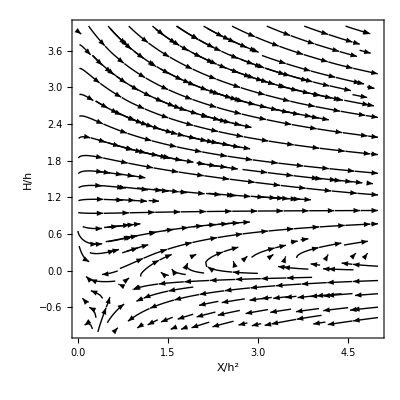

```mathematica
param={α->-1,β->1,γ->1,l->10,κ->1/2};
χyrange={χ0->10^-5,χ1->5,y0->-1,y1->4};

P1=StreamPlot[{χDSNoMat[[2]],yDSNoMat[[2]]}/.{χ[τ]->χ,y[τ]->y}/.param,{χ,χ0/.χyrange,χ1/.χyrange},{y,y0/.χyrange,y1/.χyrange},PlotTheme->"Monochrome",AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],FrameLabel->{Style["X/h^2",FontSize->16],Style["H/h",FontSize->16]},RotateLabel->False,PlotRange->{{χ0,χ1}/.χyrange,{y0,y1}/.χyrange},PerformanceGoal->"Quality"];

Show[P1]
```

We can compliment this with the curve H_C[X] where the dynamical system inadvertently blows up due to a coordinate choice. This curve is defined by...

```mathematica
HcM1=Solve[(yDSNoMat[[2]]//Denominator)==0,y[τ]];

(* number of branches *)
Length[HcM1]
```

2

The superposed phase portrait with this curve becomes...

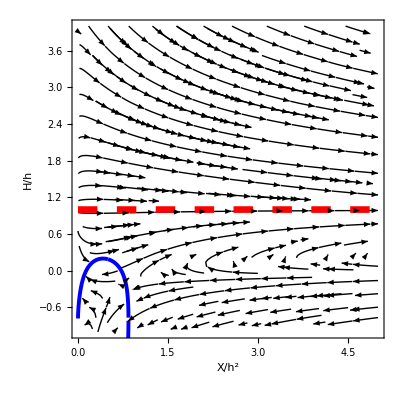

```mathematica
(* Hc *)
P2=Plot[{y[τ]/.(HcM1[[1]]/.χ[τ]->χ)/.param,y[τ]/.(HcM1[[2]]/.χ[τ]->χ)/.param},{χ,χ0/.χyrange,χ1/.χyrange},PlotStyle->{{Blue,Thickness[0.007]},{Blue,Thickness[0.007]}},Exclusions->{-(2 κ)/(3 α+β)/.param}];

(* self-tuning vacuum *)
P3=Plot[1,{χ,χ0/.χyrange,χ1/.χyrange},PlotStyle->{Red,Dashing[Large],Thickness[0.012]}];

Show[P1,P2,P3]
```

This shows that for most of the phase space, the dynamics always falls to the self-tuning vacuum (H/h=1). However, it is clear that this is not the only attractor in the dynamical system.

For comparison, we show the phase portrait in the corresponding Horndeski limit (β=0)...

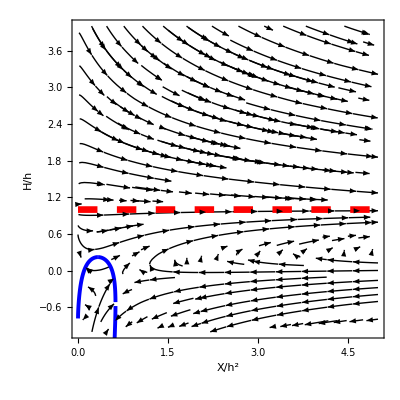

```mathematica
param={α->-1,β->0,γ->1,l->10,κ->1/2};
χyrange={χ0->10^-5,χ1->5,y0->-1,y1->4};

P1=StreamPlot[{χDSNoMat[[2]],yDSNoMat[[2]]}/.{χ[τ]->χ,y[τ]->y}/.param,{χ,χ0/.χyrange,χ1/.χyrange},{y,y0/.χyrange,y1/.χyrange},PlotTheme->"Monochrome",AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],FrameLabel->{Style["X/h^2",FontSize->16],Style["H/h",FontSize->16]},RotateLabel->False,PlotRange->{{χ0,χ1}/.χyrange,{y0,y1}/.χyrange},PerformanceGoal->"Quality"];

(* Hc *)
P2=Plot[{y[τ]/.(HcM1[[1]]/.χ[τ]->χ)/.param,y[τ]/.(HcM1[[2]]/.χ[τ]->χ)/.param},{χ,χ0/.χyrange,χ1/.χyrange},PlotStyle->{{Blue,Thickness[0.007]},{Blue,Thickness[0.007]}},Exclusions->{-(2 κ)/(3 α+β)/.param}];

(* self-tuning vacuum *)
P3=Plot[1,{χ,χ0/.χyrange,χ1/.χyrange},PlotStyle->{Red,Dashing[Large],Thickness[0.012]}];

Show[P1,P2,P3]
```

Checking out β=4...

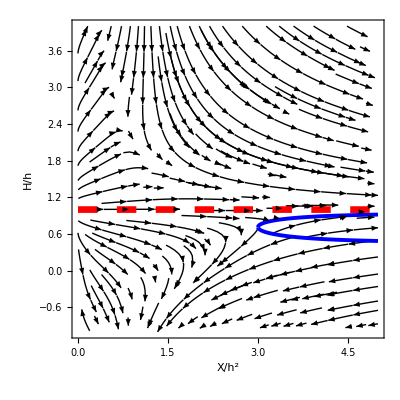

```mathematica
param={α->-1,β->4,γ->1,l->10,κ->1/2};
χyrange={χ0->10^-5,χ1->5,y0->-1,y1->4};

P1=StreamPlot[{χDSNoMat[[2]],yDSNoMat[[2]]}/.{χ[τ]->χ,y[τ]->y}/.param,{χ,χ0/.χyrange,χ1/.χyrange},{y,y0/.χyrange,y1/.χyrange},PlotTheme->"Monochrome",AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],FrameLabel->{Style["X/h^2",FontSize->16],Style["H/h",FontSize->16]},RotateLabel->False,PlotRange->{{χ0,χ1}/.χyrange,{y0,y1}/.χyrange},PerformanceGoal->"Quality"];

(* Hc *)
P2=Plot[{y[τ]/.(HcM1[[1]]/.χ[τ]->χ)/.param,y[τ]/.(HcM1[[2]]/.χ[τ]->χ)/.param},{χ,χ0/.χyrange,χ1/.χyrange},PlotStyle->{{Blue,Thickness[0.007]},{Blue,Thickness[0.007]}},Exclusions->{-(2 κ)/(3 α+β)/.param}];

(* self-tuning vacuum *)
P3=Plot[1,{χ,χ0/.χyrange,χ1/.χyrange},PlotStyle->{Red,Dashing[Large],Thickness[0.012]}];

Show[P1,P2,P3]
```

Now, we draw the phase portrait with an extreme teleparallel parameter (β=10)...

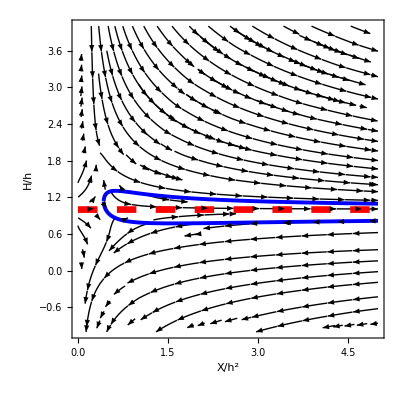

```mathematica
param={α->-1,β->10,γ->1,l->10,κ->1/2};
χyrange={χ0->10^-5,χ1->5,y0->-1,y1->4};

P1=StreamPlot[{χDSNoMat[[2]],yDSNoMat[[2]]}/.{χ[τ]->χ,y[τ]->y}/.param,{χ,χ0/.χyrange,χ1/.χyrange},{y,y0/.χyrange,y1/.χyrange},PlotTheme->"Monochrome",AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],FrameLabel->{Style["X/h^2",FontSize->16],Style["H/h",FontSize->16]},RotateLabel->False,PlotRange->{{χ0,χ1}/.χyrange,{y0,y1}/.χyrange},PerformanceGoal->"Quality"];

(* Hc *)
P2=Plot[{y[τ]/.(HcM1[[1]]/.χ[τ]->χ)/.param,y[τ]/.(HcM1[[2]]/.χ[τ]->χ)/.param},{χ,χ0/.χyrange,χ1/.χyrange},PlotStyle->{{Blue,Thickness[0.007]},{Blue,Thickness[0.007]}},Exclusions->{-(2 κ)/(3 α+β)/.param}];

(* self-tuning vacuum *)
P3=Plot[1,{χ,χ0/.χyrange,χ1/.χyrange},PlotStyle->{Red,Dashing[Large],Thickness[0.012]}];

Show[P1,P2,P3]
```

Clearly, at some critical β the overall picture of the dynamical system can drastically change in transition from Horndeski to teledeski. In all cases, the well-tempering vacuum remains to be a dynamical attractor.

#### 4.3 Compatibility with matter

In this section, we show the compatibility of the well-tempered cosmology with a matter-dominated universe. We go back to the well-tempered field equations...

```mathematica
FeqM1nd
HeqM1nd
SeqM1nd
MeqM1nd
```

-3 l ϕ[τ]+3 (6 κ λ+(3 α+β) χ[τ]+3 y[τ]^2 ((3 α+β) χ[τ]+2 κ (-1+Ω[τ])))==√2 l y[τ] (γ-√χ[τ])+12 (3 α+β) y[τ] χ[τ]

(6 √2 l y[τ] (-γ+√χ[τ]) √χ[τ])/h+(36 √χ[τ] ((3 α+β) (-1+y[τ])^2 χ[τ]+3 (1+w) κ y[τ]^2 Ω[τ]))/h-(12 √χ[τ] (-6 κ+(3 α+β) χ[τ]) y'[τ])/h+((√2 l (γ-√χ[τ]))/(h √χ[τ])-(12 (3 α+β) (-1+y[τ]) √χ[τ])/h) χ'[τ]==0

(18 √2 (3 α+β) (-1+y[τ])^2 y[τ] χ[τ]^(3/2))/h-(6 l (y[τ]^2 (γ √χ[τ]-χ[τ])+χ[τ]))/h+((12 √2 (3 α+β) (-1+y[τ]) χ[τ]^(3/2))/h+(2 l (-γ √χ[τ]+χ[τ]))/h) y'[τ]+((l γ y[τ])/(h √χ[τ])+(3 √2 (3 α+β) (-1+y[τ])^2 √χ[τ])/h) χ'[τ]==0

3 (1+w) κ y[τ]^3 Ω[τ]+2 κ y[τ] Ω[τ] y'[τ]+κ y[τ]^2 Ω'[τ]==0

Now, we numerically integrate this coupled system with the initial conditions of a matter era, i.e., H~2/(3t), Ω~1, and ϕ̇<<1. We proceed by writing everything down explicitly in terms of the fields (a,ϕ,Ω) where a is defined by y=(∂_τ a)/a...

```mathematica
FeqM1ndaϕΩ=FeqM1nd/.y->Function[τ,a'[τ]/a[τ]]/.χ->Function[τ,ϕ'[τ]^2/2]/.√(ϕ'[τ]^2)->ϕ'[τ]//Simplify;
HeqM1ndaϕΩ=HeqM1nd/.y->Function[τ,a'[τ]/a[τ]]/.χ->Function[τ,ϕ'[τ]^2/2]/.√(ϕ'[τ]^2)->ϕ'[τ]/.(ϕ'[τ]^2)^(3/2)->ϕ'[τ]^3//Simplify;
SeqM1ndaϕΩ=SeqM1nd/.y->Function[τ,a'[τ]/a[τ]]/.χ->Function[τ,ϕ'[τ]^2/2]/.√(ϕ'[τ]^2)->ϕ'[τ]/.(ϕ'[τ]^2)^(3/2)->ϕ'[τ]^3//Simplify;
MeqM1ndaϕΩ=MeqM1nd/.y->Function[τ,a'[τ]/a[τ]]//Simplify;

FeqM1ndaϕΩ
HeqM1ndaϕΩ
SeqM1ndaϕΩ
MeqM1ndaϕΩ
```

3 (6 κ λ-l ϕ[τ]+1/2 (3 α+β) ϕ'[τ]^2+(3 a'[τ]^2 (2 κ (-1+Ω[τ])+1/2 (3 α+β) ϕ'[τ]^2))/a[τ]^2)==(a'[τ] (√2 l γ-l ϕ'[τ]+6 (3 α+β) ϕ'[τ]^2))/a[τ]

1/h ϕ'[τ] ((6 l a'[τ] (-γ+ϕ'[τ]/(√2)))/a[τ]+(9 √2 (6 (1+w) κ Ω[τ] a'[τ]^2+(3 α+β) (a[τ]-a'[τ])^2 ϕ'[τ]^2))/a[τ]^2-(3 √2 (12 κ-(3 α+β) ϕ'[τ]^2) (a'[τ]^2-a[τ] a''[τ]))/a[τ]^2+2 (-3 √2 (3 α+β) (-1+a'[τ]/a[τ]) ϕ'[τ]+(l (γ-ϕ'[τ]/(√2)))/(√(ϕ'[τ]^2))) ϕ''[τ])==0

1/(h a[τ]^3 √(ϕ'[τ]^2))(9 (3 α+β) (a[τ]-a'[τ])^2 a'[τ] ϕ'[τ]^3 √(ϕ'[τ]^2)-3 l a[τ] ϕ'[τ] √(ϕ'[τ]^2) (a'[τ]^2 (√2 γ-ϕ'[τ])+a[τ]^2 ϕ'[τ])+√(ϕ'[τ]^2) (l a[τ] (√2 γ-ϕ'[τ]) ϕ'[τ]+6 (3 α+β) (a[τ]-a'[τ]) ϕ'[τ]^3) (a'[τ]^2-a[τ] a''[τ])+a[τ] ϕ'[τ] (√2 l γ a[τ] a'[τ]+3 (3 α+β) (a[τ]-a'[τ])^2 ϕ'[τ] √(ϕ'[τ]^2)) ϕ''[τ])==0

(κ a'[τ] (a[τ] a'[τ] Ω'[τ]+Ω[τ] ((1+3 w) a'[τ]^2+2 a[τ] a''[τ])))/a[τ]==0

The matter equation may now be solved for Ω[a(τ)]. This leads to...

```mathematica
ΩM1sol=DSolve[MeqM1ndaϕΩ,Ω,τ][[1]]/.C[1]->ω;

Ω[τ]==(Ω[τ]/.ΩM1sol)
```

Ω[τ]==(ω a[τ]^(-1-3 w))/a'[τ]^2

The constraint and the dynamical equations can therefore be reduced to...

```mathematica
FeqM1aϕ=FeqM1ndaϕΩ/.ΩM1sol//FullSimplify;
HeqM1aϕ=HeqM1ndaϕΩ/.ΩM1sol//FullSimplify;
SeqM1aϕ=SeqM1ndaϕΩ;

FeqM1aϕ
HeqM1aϕ
SeqM1aϕ
```

3/2 (12 κ λ+12 κ ω a[τ]^(-3 (1+w))-2 l ϕ[τ]+(3 α+β) ϕ'[τ]^2+(3 a'[τ]^2 (-4 κ+(3 α+β) ϕ'[τ]^2))/a[τ]^2)==(a'[τ] (√2 l γ-l ϕ'[τ]+6 (3 α+β) ϕ'[τ]^2))/a[τ]

1/h ϕ'[τ] ((3 l a'[τ] (-2 γ+√2 ϕ'[τ]))/a[τ]+(9 √2 (6 (1+w) κ ω a[τ]^(-1-3 w)+(3 α+β) (a[τ]-a'[τ])^2 ϕ'[τ]^2))/a[τ]^2-(3 √2 (12 κ-(3 α+β) ϕ'[τ]^2) (a'[τ]^2-a[τ] a''[τ]))/a[τ]^2+2 (-3 √2 (3 α+β) (-1+a'[τ]/a[τ]) ϕ'[τ]+(l (γ-ϕ'[τ]/(√2)))/(√(ϕ'[τ]^2))) ϕ''[τ])==0

1/(h a[τ]^3 √(ϕ'[τ]^2))(9 (3 α+β) (a[τ]-a'[τ])^2 a'[τ] ϕ'[τ]^3 √(ϕ'[τ]^2)-3 l a[τ] ϕ'[τ] √(ϕ'[τ]^2) (a'[τ]^2 (√2 γ-ϕ'[τ])+a[τ]^2 ϕ'[τ])+√(ϕ'[τ]^2) (l a[τ] (√2 γ-ϕ'[τ]) ϕ'[τ]+6 (3 α+β) (a[τ]-a'[τ]) ϕ'[τ]^3) (a'[τ]^2-a[τ] a''[τ])+a[τ] ϕ'[τ] (√2 l γ a[τ] a'[τ]+3 (3 α+β) (a[τ]-a'[τ])^2 ϕ'[τ] √(ϕ'[τ]^2)) ϕ''[τ])==0

The Hubble equation may be solved with the scalar field equation for (a,ϕ). We setup the numerical integration in the next lines. First, we got to fix the initial constraint surface...

```mathematica
FeqM1aϕMat=FeqM1aϕ/.w->0;
ℱConstraint=Collect[-((FeqM1aϕMat[[1]]-FeqM1aϕMat[[2]])/3)/.Solve[σ==3α+β,α][[1]]//Simplify,{σ,l,γ},Expand];
HeqM1aϕMat=HeqM1aϕ/.w->0;
SeqM1aϕMat=SeqM1aϕ/.w->0;

ℱConstraint==0
```

-6 κ λ-(6 κ ω)/a[τ]^3+(6 κ a'[τ]^2)/a[τ]^2+l (ϕ[τ]+(√2 γ a'[τ])/(3 a[τ])-(a'[τ] ϕ'[τ])/(3 a[τ]))+σ (-1/2 ϕ'[τ]^2+(2 a'[τ] ϕ'[τ]^2)/a[τ]-(3 a'[τ]^2 ϕ'[τ]^2)/(2 a[τ]^2))==0

The initial conditions must be chosen to respect this constraint. Also, we want Ω~1 (corresponding to an initial matter universe). We find the matter solution and the Friedmann constraint on the initial surface to then be...

```mathematica
aMat=a->Function[{τ},(3/2)^(2/3) (τ √ω+a0)^(2/3)];

Ω[τ]==(Ω[τ]/.ΩM1sol/.aMat//Simplify)
InitHSurface=FeqM1aϕMat/.aMat/.{ϕ[τ]->ϕ0,ϕ'[τ]->ϕp0}/.τ->τ0//Simplify;InitHSurface
```

Ω[τ]==(9/4)^-w (a0+τ √ω)^(-2 w)

18 κ λ-3 l ϕ0+((3 α+β) ϕp0^2 (3 a0^2+6 a0 τ0 √ω+(4+3 τ0^2) ω))/(2 (a0+τ0 √ω)^2)==(2 (√2 l γ-l ϕp0+6 (3 α+β) ϕp0^2) √ω)/(3 (a0+τ0 √ω))

To get, Ω~1 (matter universe), we select ω~(4-12 a_0+9 a_0^2)/(9 τ0^2). We then consider a_0 and ϕ_0' as the independent phase space variables of the dynamical system. ϕ_0 will be determined on this surface. Using this procedure, we compute the initial scalar ϕ_0 and the Hubble parameter for a given set of theory parameters...

```mathematica
param={λ->10^10,α->-1,β->1,γ->1,l->10,κ->1/2};
Init={a0->10,ϕp0->1};
τparam={τ0->10^-1,τf->4};
ωMatInit=ω->(4-12 a0+9 a0^2)/(9 τ0^2);

ϕ0Init=NSolve[(InitHSurface/.ωMatInit/.param/.τparam/.Init),ϕ0,Reals,WorkingPrecision->50][[1]];ϕ0Init

(* initial Hubble constant *)
y[τ0]==(a'[τ]/a[τ]/.aMat/.ωMatInit/.τ->τ0/.τparam/.Init//N)
```

{ϕ0→2.9999999976355774704096271903461867564298126043089×10^9}

y[τ0]==3.21839

The cosmological dynamics may now be solved numerically. Here is the Hubble parameter and the scalar field as a function of time...

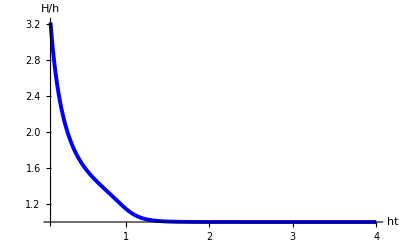

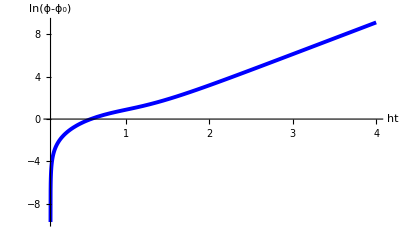

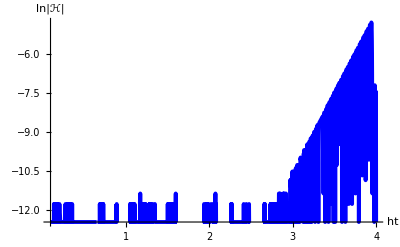

```mathematica
solMat=NDSolve[{HeqM1aϕMat,SeqM1aϕMat,a[τ0]==(a[τ0]/.aMat),a'[τ0]==(a'[τ0]/.aMat),ϕ[τ0]==ϕ0,ϕ'[τ0]==ϕp0}/.ωMatInit/.param/.τparam/.Init/.ϕ0Init,{a,ϕ},{τ,τ0,τf}/.τparam,PrecisionGoal->10,AccuracyGoal->10,WorkingPrecision->30][[1]];

(* Hubble function *)
Plot[a'[τ]/a[τ]/.solMat,{τ,τ0,τf}/.τparam,PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"ht","H/h"}]

(* scalar field *)
Plot[Log[ϕ[τ]-ϕ0]/.ϕ0Init/.solMat,{τ,τ0,τf}/.τparam,PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"ht","ln(ϕ-ϕ_0)"}]

(* Hamiltonian constraint *)
Plot[Log[Abs[ℱConstraint]]/.σ->3α+β/.ωMatInit/.Init/.τparam/.param/.solMat,{τ,τ0,τf}/.τparam,PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"ht","ln|ℋ|"}]
```

The relaxation of the system to the well tempered vacuum is evident in the next plot...

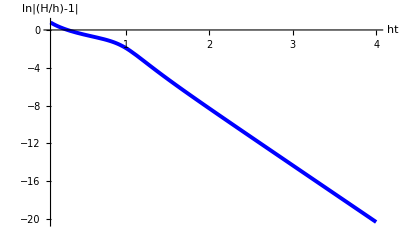

```mathematica
(* relaxation to the vacuum *)
Plot[Log[Abs[a'[τ]/a[τ]-1]]/.solMat,{τ,τ0,τf}/.τparam,PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"ht","ln|(H/h)-1|"}]
```

The density parameters of the matter and dark energy is shown in the next plot...

Ω_M==ω/(a[τ] a'[τ]^2)

Ω_ϕ^(H)==-(l a[τ] (3 a[τ] ϕ[τ]+a'[τ] (√2 γ-ϕ'[τ])))/(18 κ a'[τ]^2)

Ω_ϕ^(T)==(σ (a[τ]^2-4 a[τ] a'[τ]+3 a'[τ]^2) ϕ'[τ]^2)/(12 κ a'[τ]^2)

Ω_Λ==(λ a[τ]^2)/a'[τ]^2

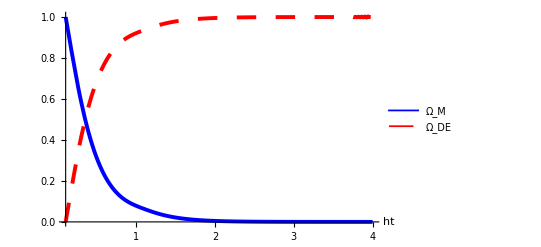

```mathematica
kHsq=6κ a'[τ]^2/a[τ]^2;
ΩMat=-ω Coefficient[ℱConstraint,ω]/kHsq;
ΩHor=-l Coefficient[ℱConstraint,l]/kHsq;
ΩTel=-σ Coefficient[ℱConstraint,σ]/kHsq;
ΩLmd=-λ Coefficient[ℱConstraint,λ]/kHsq;

"Ω_M"==ΩMat//Simplify
"Ω_ϕ^(H)"==ΩHor//Simplify
"Ω_ϕ^(T)"==ΩTel//Simplify
"Ω_Λ"==ΩLmd//Simplify

Plot[{ΩMat/.ωMatInit/.Init/.τparam/.param/.solMat,ΩHor+ΩTel+ΩLmd/.σ->3α+β/.param/.solMat},{τ,τ0,τf}/.τparam,PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]},{Red,Dashing[Large],Thickness[0.007]}},AxesLabel->{"ht",""},PlotLegends->{"Ω_M","Ω_DE"}]
```

We setup below a function which generates a solution in one go provided the given parameters...

```mathematica
WellTemper[ag_,ϕg_,λg_,αg_,βg_,γg_,lg_,τ0g_,τfg_]:=(param={λ->λg,α->αg,β->βg,γ->γg,l->lg,κ->1/2};
Init={a0->ag,ϕp0->ϕg};
τparam={τ0->τ0g,τf->τfg};
ωMatInit=ω->(4-12 a0+9 a0^2)/(9 τ0^2);

ϕ0Init=NSolve[(InitHSurface/.ωMatInit/.param/.τparam/.Init),ϕ0,Reals,WorkingPrecision->50][[1]];

nsol=NDSolve[{HeqM1aϕMat,SeqM1aϕMat,a[τ0]==(a[τ0]/.aMat),a'[τ0]==(a'[τ0]/.aMat),ϕ[τ0]==ϕ0,ϕ'[τ0]==ϕp0}/.ωMatInit/.param/.τparam/.Init/.ϕ0Init,{a,ϕ},{τ,τ0,τf}/.τparam,PrecisionGoal->10,AccuracyGoal->10,WorkingPrecision->30][[1]];NSol={nsol,param,τparam,Init,ϕ0Init,ωMatInit};NSol)
```

```mathematica
WTic1=WellTemper[10,1,10^10,-1,1,1,10,10^-1,4];
WTic2=WellTemper[1,1,10^10,-1,1,1,10,10^-1,4];
WTic3=WellTemper[1/10,1,10^10,-1,1,1,10,10^-1,4];
WTic4=WellTemper[10,10,10^10,-1,1,1,10,10^-1,4];
WTic5=WellTemper[10,1/10,10^10,-1,1,1,10,10^-1,4];
```

As an example of using this function, we show the relaxation to the self-tuning vacuum for various initial conditions...

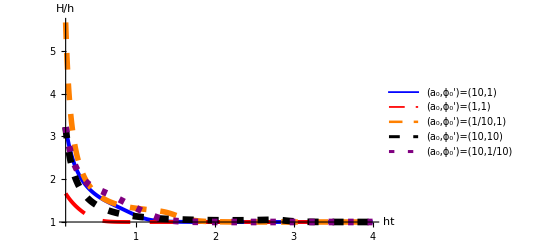

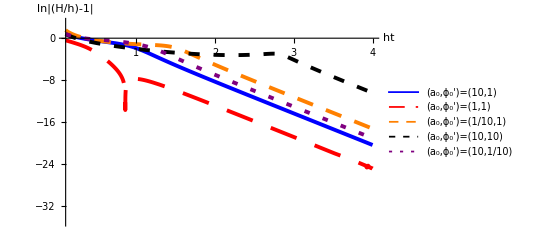

```mathematica
(* Hubble function *)
Plot[{a'[τ]/a[τ]/.WTic1[[1]],a'[τ]/a[τ]/.WTic2[[1]],a'[τ]/a[τ]/.WTic3[[1]],a'[τ]/a[τ]/.WTic4[[1]],a'[τ]/a[τ]/.WTic5[[1]]},{τ,τ0,τf}/.τparam,PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]},{Red,Dashing[{0.05,0.035}],Thickness[0.007]},{Orange,Dashing[{0.030,0.025}],Thickness[0.01]},{Black,Dashing[{0.020,0.025}],Thickness[0.012]},{Purple,Dashing[{0.010,0.025}],Thickness[0.012]}},AxesLabel->{"ht","H/h"},PlotLegends->{"(a_0,ϕ_0')=(10,1)","(a_0,ϕ_0')=(1,1)","(a_0,ϕ_0')=(1/10,1)","(a_0,ϕ_0')=(10,10)","(a_0,ϕ_0')=(10,1/10)"}]

(* exponential relaxation to the vacuum *)
Plot[{Log[Abs[a'[τ]/a[τ]-1]]/.WTic1[[1]],Log[Abs[a'[τ]/a[τ]-1]]/.WTic2[[1]],Log[Abs[a'[τ]/a[τ]-1]]/.WTic3[[1]],Log[Abs[a'[τ]/a[τ]-1]]/.WTic4[[1]],Log[Abs[a'[τ]/a[τ]-1]]/.WTic5[[1]]},{τ,τ0,τf}/.τparam,PlotRange->{All,{-35,3}},AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,13],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]},{Red,Dashing[{0.05,0.035}],Thickness[0.007]},{Orange,Dashing[{0.030,0.025}],Thickness[0.007]},{Black,Dashing[{0.020,0.025}],Thickness[0.007]},{Purple,Dashing[{0.010,0.025}],Thickness[0.007]}},AxesLabel->{"ht","ln|(H/h)-1|"},PlotLegends->Placed[{"(a_0,ϕ_0')=(10,1)","(a_0,ϕ_0')=(1,1)","(a_0,ϕ_0')=(1/10,1)","(a_0,ϕ_0')=(10,10)","(a_0,ϕ_0')=(10,1/10)"},{0.3,0.29}]]
```

The scalar and the density parameters for these cases are as follows...

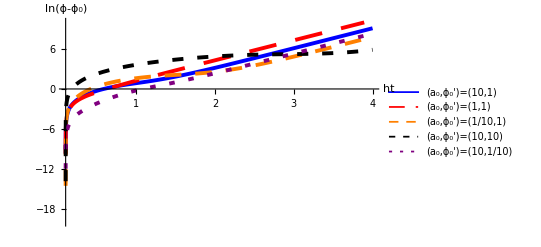

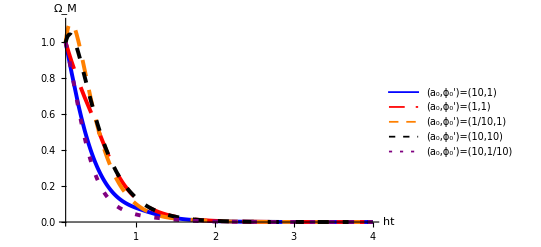

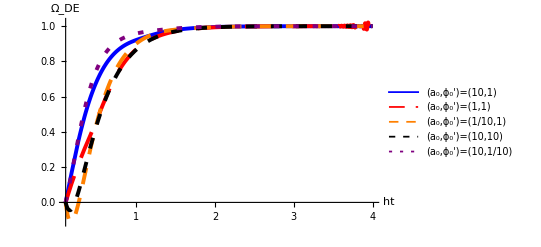

```mathematica
(* scalar field *)
Plot[{Log[ϕ[τ]-ϕ0]/.WTic1[[1]]/.WTic1[[5]],Log[ϕ[τ]-ϕ0]/.WTic2[[1]]/.WTic2[[5]],Log[ϕ[τ]-ϕ0]/.WTic3[[1]]/.WTic3[[5]],Log[ϕ[τ]-ϕ0]/.WTic4[[1]]/.WTic4[[5]],Log[ϕ[τ]-ϕ0]/.WTic5[[1]]/.WTic5[[5]]},{τ,τ0,τf}/.τparam,PlotRange->{All,{-20,10}},AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,13],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]},{Red,Dashing[{0.05,0.035}],Thickness[0.007]},{Orange,Dashing[{0.030,0.025}],Thickness[0.007]},{Black,Dashing[{0.020,0.025}],Thickness[0.007]},{Purple,Dashing[{0.010,0.025}],Thickness[0.007]}},AxesLabel->{"ht","ln(ϕ-ϕ_0)"},PlotLegends->Placed[{"(a_0,ϕ_0')=(10,1)","(a_0,ϕ_0')=(1,1)","(a_0,ϕ_0')=(1/10,1)","(a_0,ϕ_0')=(10,10)","(a_0,ϕ_0')=(10,1/10)"},{0.75,0.27}]]

(* matter density *)
Plot[{ΩMat/.WTic1[[6]]/.WTic1[[2]]/.WTic1[[3]]/.WTic1[[4]]/.WTic1[[1]],ΩMat/.WTic2[[6]]/.WTic2[[2]]/.WTic2[[3]]/.WTic2[[4]]/.WTic2[[1]],ΩMat/.WTic3[[6]]/.WTic3[[2]]/.WTic3[[3]]/.WTic3[[4]]/.WTic3[[1]],ΩMat/.WTic4[[6]]/.WTic4[[2]]/.WTic4[[3]]/.WTic4[[4]]/.WTic4[[1]],ΩMat/.WTic5[[6]]/.WTic5[[2]]/.WTic5[[3]]/.WTic5[[4]]/.WTic5[[1]]},{τ,τ0,τf}/.τparam,PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,13],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]},{Red,Dashing[{0.05,0.035}],Thickness[0.007]},{Orange,Dashing[{0.030,0.025}],Thickness[0.007]},{Black,Dashing[{0.020,0.025}],Thickness[0.007]},{Purple,Dashing[{0.010,0.025}],Thickness[0.007]}},AxesLabel->{"ht","Ω_M"},PlotLegends->Placed[{"(a_0,ϕ_0')=(10,1)","(a_0,ϕ_0')=(1,1)","(a_0,ϕ_0')=(1/10,1)","(a_0,ϕ_0')=(10,10)","(a_0,ϕ_0')=(10,1/10)"},{0.75,0.7}]]

(* dark energy density *)
Plot[{ΩHor+ΩTel+ΩLmd/.σ->3α+β/.WTic1[[2]]/.WTic1[[1]],ΩHor+ΩTel+ΩLmd/.σ->3α+β/.WTic2[[2]]/.WTic2[[1]],ΩHor+ΩTel+ΩLmd/.σ->3α+β/.WTic3[[2]]/.WTic3[[1]],ΩHor+ΩTel+ΩLmd/.σ->3α+β/.WTic4[[2]]/.WTic4[[1]],ΩHor+ΩTel+ΩLmd/.σ->3α+β/.WTic5[[2]]/.WTic5[[1]]},{τ,τ0,τf}/.τparam,PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,13],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]},{Red,Dashing[{0.05,0.035}],Thickness[0.007]},{Orange,Dashing[{0.030,0.025}],Thickness[0.007]},{Black,Dashing[{0.020,0.025}],Thickness[0.007]},{Purple,Dashing[{0.010,0.025}],Thickness[0.007]}},AxesLabel->{"ht","Ω_DE"},PlotLegends->Placed[{"(a_0,ϕ_0')=(10,1)","(a_0,ϕ_0')=(1,1)","(a_0,ϕ_0')=(1/10,1)","(a_0,ϕ_0')=(10,10)","(a_0,ϕ_0')=(10,1/10)"},{0.75,0.5}]]
```

#### 4.4 Stability through phase transitions

We test the stability of the well-tempered vacuum under phase transitions of the vacuum energy. To do so, we use the effective energy density and pressure given by...

```mathematica
ptρ=ρ->Function[t,ρΛ+(ΔρΛ/2 Tanh[(t-T)/Δt])];
ptP=P->Function[t,-ρ[t]-ρ'[t]/(3H[t])];
```

...where ρ_Λ is an initial vacuum energy that would be changed by Δρ_Λ in an interval Δt at time t~T.Here is a plot of the effective energy density and pressure...

(ρ_eff(τ))/(3 h^2)==2 κ λ+Δλ κ Tanh[(τ-Τ)/Δτ]

(P_eff(τ))/(3 h^2)==-2 κ λ-(Δλ κ Sech[(τ-Τ)/Δτ]^2)/(3 Δτ)-Δλ κ Tanh[(τ-Τ)/Δτ]

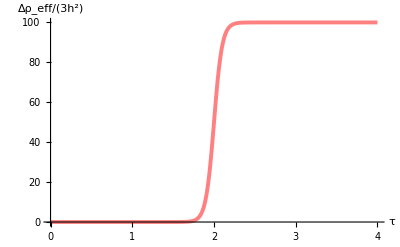

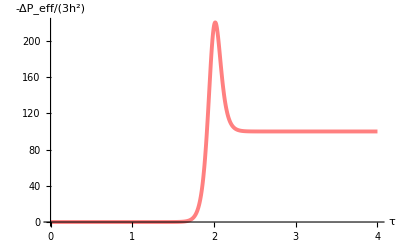

```mathematica
ρnd[τ_]=(ρ[t]/.ptρ/.{t->h τ,T->h Τ,Δt->h Δτ,ρΛ->6κ h^2 λ,ΔρΛ->6κ h^2 Δλ}//Simplify);
Pnd[τ_]=(P[t]/.ptP/.ptρ/.H[t]->h/.{t->h τ,T->h Τ,Δt->h Δτ,ρΛ->6κ h^2 λ,ΔρΛ->6κ h^2 Δλ}//Simplify);

"(ρ_eff(τ))/(3 h^2)"==ρnd[τ]/(3 h^2)//Expand
"(P_eff(τ))/(3 h^2)"==Pnd[τ]/(3 h^2)/.h->1//Expand

Plot[{(ρnd[τ]-ρnd[0])/(3 h^2)/.Solve[λi==λ-Δλ/2,λ][[1]]/.κ->1/2/.{λi->10^10,Δλ->10^2,Τ->2,Δτ->1/10}},{τ,0,4},PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","Δρ_eff/(3h^2)"}]

Plot[{-(Pnd[τ]-Pnd[0])/(3 h^2)/.Solve[λi==λ-Δλ/2,λ][[1]]/.κ->1/2/.h->1/.{λi->10^10,Δλ->10^2,Τ->2,Δτ->1/10}},{τ,0,4},PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Thickness[0.007],Pink}},AxesLabel->{"τ","-ΔP_eff/(3h^2)"}]
```

We numerically integrate the Friedmann equations with this source term. We prepare the dimensionless dynamical system in the next lines...

```mathematica
ndpt={T->Τ,Δt->Δτ,ρΛ->6κ h^2 λ,ΔρΛ->6κ h^2 Δλ};

FeqM1pt=Collect[(FeqM1[[1]]-FeqM1[[2]])/h^3/.ptρ/.nd/.ndpt//Simplify,{y'[τ],χ'[τ],Ω'[τ],l},FullSimplify]==0;
HeqM1pt=Collect[HeqM1[[1]]-HeqM1[[2]]/.ptP/.ptρ/.nd/.ndpt/.h->1//Simplify,{y'[τ],χ'[τ],Ω'[τ],l},FullSimplify]==0;

FeqM1pt
HeqM1pt
```

9 κ (2 λ+Δλ Tanh[(τ-Τ)/Δτ]-2 y[τ]^2)+l (-3 ϕ[τ]+√2 y[τ] (-γ+√χ[τ]))+3 (3 α+β) (-1+y[τ]) (-1+3 y[τ]) χ[τ]==0

6 √2 l y[τ] (-γ+√χ[τ]) √χ[τ]+(18 √χ[τ] (-Δλ κ Sech[(τ-Τ)/Δτ]^2+2 (3 α+β) Δτ (-1+y[τ])^2 y[τ] χ[τ]))/(Δτ y[τ])-12 √χ[τ] (-6 κ+(3 α+β) χ[τ]) y'[τ]+(√2 l (-1+γ/(√χ[τ]))-12 (3 α+β) (-1+y[τ]) √χ[τ]) χ'[τ]==0

The integration proceeds in similar fashion with the previous section. We choose the initial conditions on the Hamiltonian constraint and then evolve the solution forward.

The explicit equations are prepared below...

```mathematica
FeqM1ptyϕ=FeqM1pt/.χ->Function[τ,ϕ'[τ]^2/2]/.√(ϕ'[τ]^2)->ϕ'[τ]//Simplify;
HeqM1ptyϕ=HeqM1pt/.χ->Function[τ,ϕ'[τ]^2/2]/.√(ϕ'[τ]^2)->ϕ'[τ]//Simplify;
SeqM1ptyϕ=SeqM1nd/.χ->Function[τ,ϕ'[τ]^2/2]/.√(ϕ'[τ]^2)->ϕ'[τ]/.(ϕ'[τ]^2)^(3/2)->ϕ'[τ]^3//Simplify;

FeqM1ptyϕ
HeqM1ptyϕ
SeqM1ptyϕ
```

9 κ (2 λ+Δλ Tanh[(τ-Τ)/Δτ]-2 y[τ]^2)+3/2 (3 α+β) (-1+y[τ]) (-1+3 y[τ]) ϕ'[τ]^2==l (3 ϕ[τ]+y[τ] (√2 γ-ϕ'[τ]))

ϕ'[τ] (6 l y[τ] (-γ+ϕ'[τ]/(√2))-6 √2 y'[τ] (-6 κ+1/2 (3 α+β) ϕ'[τ]^2)+(9 √2 (-Δλ κ Sech[(τ-Τ)/Δτ]^2+(3 α+β) Δτ (-1+y[τ])^2 y[τ] ϕ'[τ]^2))/(Δτ y[τ])+√2 (-6 (3 α+β) (-1+y[τ]) ϕ'[τ]+l (-1+(√2 γ)/(√(ϕ'[τ]^2)))) ϕ''[τ])==0

1/h ϕ'[τ] (9 (3 α+β) (-1+y[τ])^2 y[τ] ϕ'[τ]^2-3 l (y[τ]^2 (√2 γ-ϕ'[τ])+ϕ'[τ])+y'[τ] (-√2 l γ+l ϕ'[τ]+6 (3 α+β) (-1+y[τ]) ϕ'[τ]^2)+(3 (3 α+β) (-1+y[τ])^2 ϕ'[τ]+(√2 l γ y[τ])/(√(ϕ'[τ]^2))) ϕ''[τ])==0

Now, choosing the model parameters and the phase transition parameters, we make all things explicit. We fix the initial conditions on constraint surface...

```mathematica
InitHSurfacept=FeqM1ptyϕ/.{y[τ]->y0,ϕ[τ]->ϕ0,ϕ'[τ]->ϕp0}/.τ->τ0;InitHSurfacept
```

3/2 (-1+y0) (-1+3 y0) (3 α+β) ϕp0^2+9 κ (-2 y0^2+2 λ+Δλ Tanh[(-Τ+τ0)/Δτ])==l (3 ϕ0+y0 (√2 γ-ϕp0))

To demonstrate this, we obtain ϕ_0 for the following parameters...

```mathematica
param={α->-1,β->1,γ->1,l->10,κ->1/2};
λiToλ=Solve[λi==λ-Δλ/2,λ][[1]];
ptparam={λi->10^10,Δλ->10^2,Τ->2,Δτ->1/10};
τparam={τ0->10^-1,τf->4};
Init={y0->101/100,ϕp0->1};

ϕ0Init=NSolve[(InitHSurfacept/.param/.λiToλ/.ptparam/.τparam/.Init),ϕ0,Reals,WorkingPrecision->100][[1]];ϕ0Init
```

{ϕ0→2.999999999552488100667725608643269077258260697106881137759163403384233624398848978108539979321872563×10^9}

The dynamical system is now ready to be evolved. Here we go...

```mathematica
solpt=NDSolve[{HeqM1ptyϕ,SeqM1ptyϕ,y[τ0]==y0,ϕ[τ0]==ϕ0,ϕ'[τ0]==ϕp0}/.param/.λiToλ/.ptparam/.τparam/.Init/.ϕ0Init,{y,ϕ},{τ,τ0,τf}/.τparam,PrecisionGoal->20,AccuracyGoal->20,WorkingPrecision->50][[1]];
```

The Hubble function and the scalar field are shown below...

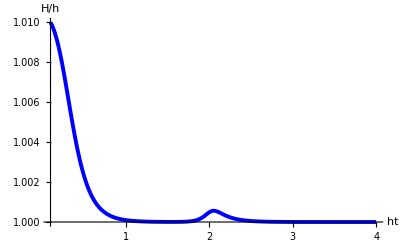

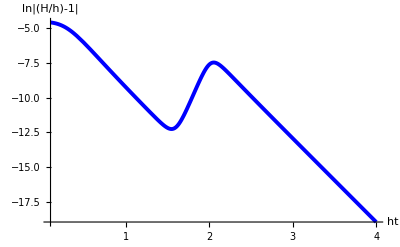

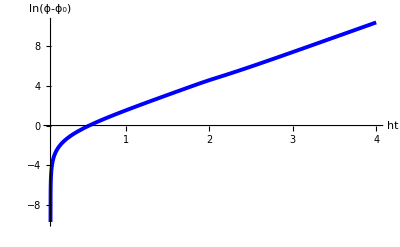

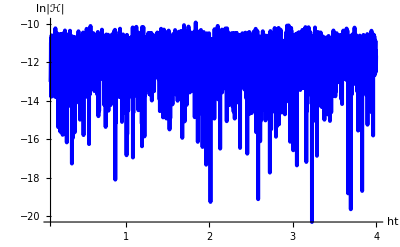

```mathematica
(* Hubble function *)
Plot[y[τ]/.solpt,{τ,τ0,τf}/.τparam,PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"ht","H/h"}]

(* relaxation to the vacuum *)
Plot[Log[Abs[y[τ]-1]]/.solpt,{τ,τ0,τf}/.τparam,PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"ht","ln|(H/h)-1|"}]

(* scalar field *)
Plot[Log[ϕ[τ]-ϕ0]/.ϕ0Init/.solpt,{τ,τ0,τf}/.τparam,PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"ht","ln(ϕ-ϕ_0)"}]

(* Hamiltonian constraint *)
Plot[Log[Abs[FeqM1ptyϕ[[1]]-FeqM1ptyϕ[[2]]]]/.param/.λiToλ/.ptparam/.solpt,{τ,τ0,τf}/.τparam,PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"ht","ln|ℋ|"}]
```

The asymptotic vacuum states can also be drawn in the Hubble relaxation plots. Recall from the linear stability analysis that δH~e^(-6τ). This is shown below...

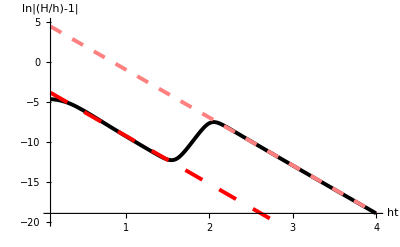

```mathematica
P1=Plot[Log[Abs[y[τ]-1]]/.solpt,{τ,τ0,τf}/.τparam,PlotRange->All,AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotStyle->{{Black,Thickness[0.007]}},AxesLabel->{"ht","ln|(H/h)-1|"}];

P2=Plot[A-6τ/.A->-3.2,{τ,τ0,τf}/.τparam,PlotStyle->{{Red,Dashing[Large],Thickness[0.007]}}];
P3=Plot[A-6τ/.A->5.1,{τ,τ0,τf}/.τparam,PlotStyle->{{Pink,Dashing[Medium],Thickness[0.007]}}];

Show[P1,P2,P3,PlotRange->{{τ0/.τparam,τf/.τparam},{-20, 5}}]
```